## Initialization

### Setup: Configuration of fixed parameters

```mathematica
config={κ->Sqrt[2 0.5],A0->(Sqrt[4*10^14/(3.5*10^16)]/0.057),E0->Sqrt[4*10^14/(3.5*10^16)],ω->0.057,Ip->0.5}  (* κ = √(2 Ip), Hydrogen, λ = 800nm, A0 = E0/ω, Intensity = 4×10^14 W/cm^2*)
```

{κ→1.,A0→1.87552,E0→0.106904,ω→0.057,Ip→0.5}

```mathematica
TC=(2 π)/ω/.config; (*one optical cycle*)
```

### Field definitions

#### vector potential for constant input intensity (using mixing angle θ)

```mathematica
potA[ωt_,θ_,"X"]:=-A0 Cos[θ] Sin[ωt]+1/2 A0 Sin[2 ωt] Sin[θ]
```

```mathematica
field1[ωt_,θ_,"X"]=E0 Cos[θ] Cos[ωt] ;
field2[ωt_,θ_,"X"]=-E0 Cos[2 ωt] Sin[θ];
combinedfield[ωt_,θ_,"X"]:=E0 Cos[θ] Cos[ωt]-E0 Cos[2 ωt] Sin[θ];
```

```mathematica
Upond[θx_,"X"]:=
(*Upond[θx,"X"]=*)
Block[{A01,A02,Upond},
A01=-Cos[θ] E0/ω; A02=1/2 Sin[θ] E0/ω;
Upond=(A01^2/4+A02^2/4)/. config;
Return[Upond/. θ->θx]]
```

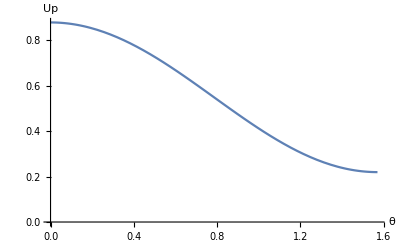

```mathematica
Plot[Upond[θx,"X"],{θx,0,π/2},AxesLabel->{"θ","Up"},AxesOrigin->{0,0}]
```

```mathematica
-D[-A0 Cos[θ] Sin[ω t]+1/2 A0 Sin[2 ω t] Sin[θ],t]/.A0 ω->E0
```

E0 Cos[θ] Cos[t ω]-E0 Cos[2 t ω] Sin[θ]

```mathematica
DynamicModule[{potential,Efield1,Efield2,Efield,A0=1, E0=1},
potential=potA[ωt,θ,"X"]/.A0->1;
Efield1=E0 Cos[θ] Cos[ωt] ;
Efield2=-E0 Cos[2 ωt] Sin[θ];
Efield=E0 Cos[θ] Cos[ωt]-E0 Cos[2 ωt] Sin[θ];
Manipulate[
Plot[{Efield1/.θ->θx, Efield2/.θ->θx,Efield/.θ->θx,potential/.θ->θx}
,{ωt,-π,2π}
, PlotStyle->{Directive[Dashed,Red],Directive[Dashed,Blue],Directive[Thick,Black],Directive[Green]}
, PlotLegends->{"E1","E2","combined field","potential"}
,GridLines->{{-3/5 π,2/3 π,2π-3/5 π,3/5 π},None}
,PlotRange->{{-π,2π},{-1.5,1}}
]
,{{θx,0.2},0,π/2}
]
]
```

#### vector potential for constant Up (using R)

```mathematica
potA[ωt_,R_,"Y"]:=A0/(√(1+R^2))(-Sin[ωt]+ R Sin[2 ωt])
```

```mathematica
Upond[Rx_,"Y"]:=Block[{A01,A02,Upond},
A01=-1/(√(1+R^2))E0/ω; A02=1/(√(1+R^2)) R E0/ω;
Upond=(A01^2/4+A02^2/4)/. config;
Return[Upond/. R->Rx]]
```

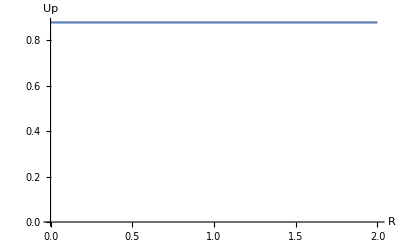

```mathematica
Plot[Upond[Rx,"Y"],{Rx,0,2},AxesLabel->{"R","Up"},AxesOrigin->{0,0}]
```

```mathematica
-D[(E0/ω)/(√(1+R^2))(-Sin[ω t]+ R Sin[2 ω t]),t]
```

-(E0 (-ω Cos[t ω]+2 R ω Cos[2 t ω]))/(√(1+R^2) ω)

```mathematica
DynamicModule[{potential,Efield1,Efield2,Efield,A0=1,E0=1},
potential=A0/(√(1+R^2))(-Sin[ωt]+ R Sin[2 ωt]);
Efield1=E0/(√(1+R^2))Cos[ωt];
Efield2=-(E0 2 R)/(√(1+R^2))Cos[2 ωt];
Efield=E0/(√(1+R^2))( Cos[ωt]-2 R Cos[2 ωt]);
Manipulate[
Plot[{Efield1/.R->Rx, Efield2/.R->Rx,Efield/.R->Rx,potential/.R->Rx}
,{ωt,-π,2π}
, PlotStyle->{Directive[Dashed,Red],Directive[Dashed,Blue],Directive[Thick,Black],Directive[Green]}
,PlotRange->{{-π,2π},{-1.5,1}}
, PlotLegends->{"E1","E2","combined field","potential"}
]
,{{Rx,0.2},0,2}
]
]
```

### Action and its derivatives

Comment on the notation used: f[a_,b_] denotes the symbolic expression (e.g. when used to find derivatives analytically), whereas f[ax_,bx_] will evaluate the function for the given numerical values ax, bx,....

#### Action

```mathematica
Sv::usage="Sv[ωt,constant] returns the symbolic form of the action.
Sv[ωt,Rx/θx,px,constant] returns the numerical value of the action for parameters Rx/θ, px at phase ωtx in the given definition of the potential.
";
```

```mathematica
Sv[ωt_,constant_?StringQ]:=
Sv[ωt,constant]=
Block[{IntPot,IntPotsq,cx,potential,action},
potential=potA[ωt,cx,constant];
IntPot=Integrate[potential,ωt];
IntPotsq=Integrate[potential*potential,ωt];
action=(1/2 (p^2 ωt +2 p IntPot+IntPotsq) +1/2 κ^2 ωt)/.cx->Which[
constant=="X",θ,
constant=="Y",R,
True,Print["OMG! I chose a undefined constant for the potential"]
];
Return[action]
]
```

```mathematica
Sv::wrongConstant="The given value for the 'constant' field `1` is not recognized.";
```

```mathematica
Message[Sv::wrongConstant,constant]
```

```mathematica
Sv[ωtx_?NumericQ,cx_?NumericQ,px_?NumericQ,constant_?StringQ]:=
Sv[ωtx,cx,px,constant]=
Sv[ωt,constant]/.{
Which[constant=="X",θ,constant=="Y",R,True,Print["OMG! I chose an undefined constant for the potential"]]->cx,
ωt->ωtx,
p->px
}/.config;
```

```mathematica
Sv[0.5+3ⅈ,0.5,0.1,"X"]
```

-496.03+429.724 ⅈ

```mathematica
Sv[ωt, "X"]
```

(κ^2 ωt)/2+1/2 (p^2 ωt+2 p (A0 Cos[θ] Cos[ωt]-1/2 A0 Cos[ωt]^2 Sin[θ])+1/96 A0^2 (-48 Cos[θ] Sin[θ] Sin[ωt]+48 Cos[θ]^2 (ωt-Cos[ωt] Sin[ωt])+8 Sin[2 θ] Sin[3 ωt]-3 Sin[θ]^2 (-4 ωt+Sin[4 ωt])))

#### First derivative

```mathematica
dSvdωt[ωt_,"X"]=D[Sv[ωt,"X"],ωt]  (*First derivative of the action. *)
```

κ^2/2+1/2 (p^2+2 p (-A0 Cos[θ] Sin[ωt]+A0 Cos[ωt] Sin[θ] Sin[ωt])+1/96 A0^2 (-48 Cos[θ] Cos[ωt] Sin[θ]-3 (-4+4 Cos[4 ωt]) Sin[θ]^2+24 Cos[3 ωt] Sin[2 θ]+48 Cos[θ]^2 (1-Cos[ωt]^2+Sin[ωt]^2)))

```mathematica
dSvdωt[ωtx_,θx_,px_,"X"]:=dSvdωt[ωtx,θx,px,"X"]=
dSvdωt[ωt,"X"]/.{θ->θx,p->px,ωt->ωtx}/.config;
```

```mathematica
dSvdωt[ωt_,"Y"]=D[Sv[ωt,"Y"],ωt]
```

κ^2/2+1/2 (p^2+(A0^2 (12+12 R^2-24 R Cos[ωt]-12 Cos[2 ωt]+24 R Cos[3 ωt]-12 R^2 Cos[4 ωt]))/(24 (1+R^2))+(2 A0 p (-Sin[ωt]+2 R Cos[ωt] Sin[ωt]))/(√(1+R^2)))

```mathematica
dSvdωt[ωtx_,Rx_,px_,"Y"]:=dSvdωt[ωt,"Y"]/.{R->Rx,p->px,ωt->ωtx}/.config;
```

#### Second derivative

```mathematica
d2Svdωt2[ωt_,"X"]=D[Sv[ωt,"X"],{ωt,2}] (*Second derivative of the action. *)
```

1/2 (2 p (-A0 Cos[θ] Cos[ωt]-1/2 A0 Sin[θ] (-2 Cos[ωt]^2+2 Sin[ωt]^2))+1/96 A0^2 (192 Cos[θ]^2 Cos[ωt] Sin[ωt]+48 Cos[θ] Sin[θ] Sin[ωt]-72 Sin[2 θ] Sin[3 ωt]+48 Sin[θ]^2 Sin[4 ωt]))

```mathematica
d2Svdωt2[ωtx_,θx_,px_,"X"]:=d2Svdωt2[ωt,"X"]/.{θ->θx,p->px,ωt->ωtx}/.config;
```

```mathematica
d2Svdωt2[ωt_,"Y"]=D[Sv[ωt,"Y"],{ωt,2}]
```

1/2 ((2 A0 p (-Cos[ωt]-R (-2 Cos[ωt]^2+2 Sin[ωt]^2)))/(√(1+R^2))+(A0^2 (24 R Sin[ωt]+24 Sin[2 ωt]-72 R Sin[3 ωt]+48 R^2 Sin[4 ωt]))/(24 (1+R^2)))

```mathematica
d2Svdωt2[ωtx_,Rx_,px_,"Y"]:=d2Svdωt2[ωt,"Y"]/.{R->Rx,p->px,ωt->ωtx}/.config;
```

### Checking the boundaries for the saddle point search and classification

#### Field minimum

I shall search in between where the field goes through zero / the potential has a maximum

```mathematica
Findωtmin[θx_,"X"]:=
Findωtmin[θx,"X"]=
Module[{startrange,starttime,inrange,zeros},
(*FIELD:  Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]*)
startrange={(-3π)/4,-π/2};
zeros=DeleteDuplicates[Select[ωt/.
Quiet@NSolve[Identity[(Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]/.θ->θx)]==0,ωt]/.C[1]->{0,-1}//Flatten
, Abs[Im[#]]<10^-5&], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
(*Print[zeros];*)
inrange=Select[zeros,startrange[[1]]<=Re[Round[#,10^-5]]<=startrange[[2]]&];
starttime=If[
Length[inrange]==1,
inrange[[1]],
Select[zeros-π,startrange[[1]]<=Re[Round[#,10^-5]]<=startrange[[2]]&][[1]]];
Return[starttime]
]
```

```mathematica
Block[{startrange,starttime,inrange,zeros,θx=0.15329846548303458},
startrange={(-3π)/4,-π/2};
zeros=DeleteDuplicates[Select[{ωt,ωt-π}/.
Quiet@NSolve[Abs[(Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]/.θ->θx)]==0,ωt]//Flatten
, Abs[Im[#]]<10^-5&], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
Print[zeros];
inrange=Select[zeros,startrange[[1]]<=Re[Round[#,10^-5]]<=startrange[[2]]&];
Print[inrange];
starttime=If[
Length[inrange]==1,
inrange[[1]],
Select[zeros-π,startrange[[1]]<=Re[Round[#,10^-5]]<=startrange[[2]]&][[1]]]
]
```

{-1.7191,-4.8607,1.7191,-1.42249}

{-1.7191}

-1.7191

#### Finding the border between the two bands

```mathematica
FindωtBorder[θx_,"X"]:=
FindωtBorder[θx,"X"]=
Module[{borderrange,bordertime,zeros},
(*FIELD:  Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]*)
borderrange={π/2,(3π)/4};
zeros=Select[ωt/.
Quiet@NSolve[Identity[(Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]/.θ->θx)]==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&];
bordertime=Select[zeros, borderrange[[1]]<=Re[Round[#,10^-5]]<=borderrange[[2]]&][[1]];
Return[bordertime]
]
```

```mathematica
Block[{θx=π/2},
Select[ωt/.
Quiet@NSolve[Identity[(Cos[θ] Cos[ωt]-Cos[2 ωt] Sin[θ]/.θ->θx)]==0,ωt]/.C[1]->{0,1}//Flatten
, Abs[Im[#]]<10^-5&]
]
```

{-0.785398,2.35619,0.785398,3.92699}

```mathematica
π/4//N
```

0.785398

```mathematica
{π/2,(3π)/4}//N
```

{1.5708,2.35619}

### Finding critical points numerically

#### Grid of seeds

```mathematica
SeedsGrid[Rx_?(Element[#,Reals]&),"Y"]:=Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,-3/5 π,7/5 π,0.5},
{ωtimag0,0,If[Rx<0.1,5π,6/5 π],0.5}
],1]
```

```mathematica
SeedsGrid[θx_?(Element[#,Reals]&),"X"]:=Module[{ωtmin},
ωtmin=Findωtmin[θx,"X"];
Flatten[Table[
ωtreal0+ⅈ ωtimag0,
{ωtreal0,ωtmin,ωtmin+2π,(2π)/10},
{ωtimag0,0,If[θx<0.1,5π,6/5 π],0.5}
],1]
]
```

#### Saddle Points (dSvdωt = 0): FindSaddles()

```mathematica
FindSaddles::usage="FindSaddles[R,p] searches for solutions of the first derivative of the action within a phase-window specified by SeedsGrid[R]. It return a list of phase values, ordered by their real part.";

FindSaddles[Rx_,px_,"Y"]:=Module[{allsolutions,solutions,seeds},
seeds=SeedsGrid[Rx,"Y"];
allsolutions = Block[{R=Rx,p=px},Table[ωtx/.
Quiet@FindRoot[
dSvdωt[ωtx,Rx,px,"Y"]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
DeleteCases[solutions,{}];

solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Abs[dSvdωt[#,Rx,px,"Y"]]<10^-5&];
solutions=Select[solutions,And[Im[#]>0,Min[Re[seeds]]<=Re[#]<Max[Re[seeds]]]&];
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]

FindSaddles[θx_,px_,"X"]:=
FindSaddles[θx,px,"X"]=
Module[{allsolutions,solutions,seeds},
seeds=SeedsGrid[θx,"X"];
allsolutions = Block[{θ=θx,p=px},Table[ωtx/.
Quiet@FindRoot[
dSvdωt[ωtx,θx,px,"X"]==0,
{ωtx,ωtSeed}],
{ωtSeed,seeds}
]];
(*DeleteCases[solutions,{}];*)
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
(*Print[Abs[dSvdωt[#,θx,px,"X"]]&/@solutions];*)
solutions=Select[solutions,Abs[dSvdωt[#,θx,px,"X"]]<10^-5&];
solutions=Select[solutions,And[Im[#]>0,Min[Re[seeds]]<=Re[#]<Max[Re[seeds]]]&];
solutions=SortBy[solutions,Re[#]&];
Return[solutions]
]
```

```mathematica
FindSaddles[π/2,0.2,"X"]
```

{-1.49801+0.467656 ⅈ,-0.0727875+0.467656 ⅈ,1.64358+0.467656 ⅈ,3.06881+0.467656 ⅈ}

```mathematica
FindRoot[
dSvdωt[ωtx,π/2,0.2,"X"]==0,
{ωtx,-2.356+0.1 ⅈ}]
```

{ωtx→-1.49801-0.467656 ⅈ}

#### Inflection points (d2Svdωt2 = 0): FindInflections()

```mathematica
FindInflections::usage="FindInflections[R,p] searches for solutions of the second derivative of the action within a phase-window specified by SeedsGrid[R]. It return a list of phase values, ordered by their real part.";

FindInflections[Rx_,px_,"Y"]:=Module[{allsolutions,solutions,seeds},
seeds=SeedsGrid[Rx,"Y"];
allsolutions = Block[{R=Rx,p=px},Table[ωt/.
Quiet@FindRoot[
d2Svdωt2[ωt,Rx,px,"Y"]==0,
{ωt,ωtSeed}],
{ωtSeed,seeds}
]];
(*it is important to keep the order in the selection process here! Because if I consider points where Im(ωt)≈0, then I still want them to have Im(ωt)>0, as I might use that for a selection process later on*)
DeleteCases[allsolutions,{}];
solutions=Select[Flatten[allsolutions,1],Im[#]>0&];
solutions=DeleteDuplicates[solutions,  Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Min[Re[seeds]]<=Re[#]<Max[Re[seeds]]&];

Return[SortBy[solutions,Re[#]&]]
]
```

```mathematica
FindInflections[θx_,px_,"X"]:=Module[{allsolutions,solutions,seeds},
seeds=SeedsGrid[θx,"X"];
allsolutions = Block[{θ=θx,p=px},Table[ωt/.
Quiet@FindRoot[
d2Svdωt2[ωt,θx,px,"X"]==0,
{ωt,ωtSeed}],
{ωtSeed,seeds}
]];
(*it is important to keep the order in the selection process here! Because if I consider points where Im(ωt)≈0, then I still want them to have Im(ωt)>0, as I might use that for a selection process later on*)
DeleteCases[allsolutions,{}];
solutions=Select[Flatten[allsolutions,1],Im[#]>0&];
solutions=DeleteDuplicates[solutions,  Function[{ωt1,ωt2},Abs[ωt1-ωt2]<10^-5]];
solutions=Select[solutions,Min[Re[seeds]]<=Re[#]<Max[Re[seeds]]&];

Return[SortBy[solutions,Re[#]&]]
]
```

```mathematica
FindInflections[0.2,0.1,"Y"]
```

{-0.025822+1.56789 ⅈ,-6.35125×10^-17+1.02152 ⅈ,0.0905011+6.00947×10^-22 ⅈ,1.89518+3.63119×10^-23 ⅈ,3.10274+2.55296×10^-16 ⅈ}

#### FoldPoint (dSvdωt = d2Svdωt2 = 0)

```mathematica
FoldPoint::usage="FoldPoint. This searches for solutions of the first derivative of the action at points where the second derivative is zero as well. It returns the respective saddle point as an association.";

FoldPointR=Block[{Rx,px=0,special,drv1,Rcrit},
(*we calculate all inflection points for given Rx and choose the one with minimal imaginary part*)
special[Rx_?NumericQ]:=MinimalBy[
Select[
FindInflections[Rx,px,"Y"]
,Abs[Re[#]]<0.1&&Im[#]>0.1&]
,Im];
(*this yields the value of the first derivative at the found inflection point*)
drv1[Rx_?NumericQ]:=dSvdωt[special[Rx],Rx,px,"Y"];

(*we want to find the R value where drv1 is zero (= where the inflection point is also a saddle point)*)
Rcrit=Re[R]/.Quiet@FindRoot[
drv1[R]
,{R,0.1}];

<|"Order"->12,"R"->Rcrit,"ωt"->special[Rcrit][[1]],"p"->px|>
]
```

<|Order→12,R→0.178251,ωt→-3.87578×10^-17+1.12114 ⅈ,p→0|>

```mathematica
FoldPointθ=Block[{θx,px=0,special,drv1,θcrit},
(*we calculate all inflection points for given θx and choose the one with minimal imaginary part*)
special[θx_?NumericQ]:=MinimalBy[
Select[
FindInflections[θx,px,"X"]
,Abs[Re[#]]<0.1&&Im[#]>0.1&]
,Im];
(*this yields the value of the first derivative at the found inflection point*)
drv1[θx_?NumericQ]:=dSvdωt[special[θx],θx,px,"X"];

(*we want to find the R value where drv1 is zero (= where the inflection point is also a saddle point)*)
θcrit=Re[θ]/.Quiet@FindRoot[
drv1[θ]
,{θ,0.3}];

<|"Order"->12,"θ"->θcrit,"ωt"->special[θcrit][[1]],"p"->px|>
]
```

<|Order→12,θ→0.333955,ωt→5.1276×10^-29+1.14485 ⅈ,p→0|>

#### test - find fold for non-zero p

```mathematica
FindFold[px_]:=FindFold[px]=Module[{allsolutions,solutions,seeds},
seeds=Union[SeedsGrid[0],SeedsGrid[1]];
allsolutions = Block[{p=px},
Table[{Rx,ωt}/.
FindRoot[
{dSvdωt[ωt,Rx,px]==0,
d2Svdωt2[ωt,Rx,px]==0},
{{ωt,ωtSeed},{Rx,Rx0}}],
{Rx0,0,1,0.1},
{ωtSeed,seeds}
]];
solutions=DeleteDuplicates[Flatten[allsolutions,1], Function[{p1,p2},And[Abs[p1[[1]]-p2[[1]]]<10^-5, Abs[p1[[2]]-p2[[2]]]<10^-5]]];

solutions=Select[solutions,And[
0<=Re[#[[1]]]<=1, (*bounds for R*)
Im[#[[2]]]>0,
Min[Re[seeds]]<=Re[#[[2]]]<Max[Re[seeds]]
]&];

 (*make sure that it  actually solves the second drv*)
solutions=Select[solutions,Abs[d2Svdωt2[#[[2]],#[[1]],px]]<10^-5&];

DeleteCases[solutions,{}];
Return[solutions]
]
```

### Plotting utilities

#### Colors for labels

```mathematica
LabelColors=<|"A"->Lighter[RGBColor[0.92, 0.16, 0.05],0.15],"B"->RGBColor[0, 0.9, 0.13],"C"->Darker[RGBColor[0, 0.4, 0.875],0.15],"D"->RGBColor[1, 0.9, 0]|>
```

<|A→RGBColor[0.932, 0.28600000000000003, 0.1925],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0., 0.34, 0.74375],D→RGBColor[1, 0.9, 0]|>

#### PlotSaddlesAsSpheres ()

```mathematica
PlotSaddlesAsSpheres[saddleslist_,constant_?StringQ]:=Module[{ckey},
ckey=Which[constant=="X","θ",constant=="Y","R",True,"ERROR"];
Graphics3D[{
Function[{
LabelColors[#[["label"]]],
Ellipsoid[{Re[#[["ωt"]]],
#[[ckey]]
,Im[#[["ωt"]]]},{1,1/3,1}×0.05]
}]/@saddleslist
}]
]
```

### ClassifySaddles() Functions

#### ClassifySaddles()

```mathematica
ClassifySaddles[saddlesList_,θx_,"X"]:=ClassifySaddles[saddlesList,θx,"X","ω"];
```

#### ω - centric : ClassifySaddles() (“vertical”)

```mathematica
ClearAll[ClassifySaddles]
```

ClearAlle[ClassifySaddles]

```mathematica
ClassifySaddles[saddlesList_,θx_,"X","ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,
classifiedsaddles,
ωtmin,ωtborder,test
},
ωtmin=Findωtmin[θx,"X"];
ωtborder=FindωtBorder[θx,"X"];
(*Print[ωtborder];*)
saddles=SortBy[Select[saddlesList,ωtmin<=Re[#]<=ωtmin+2π&],Re[#]&]; (*Redundant but kept for safety*)
(*Selecting the three saddle points in the first band, sorting them by their imaginary part, and - if ambiguous - by inverse real part. 
The latter is the case for R > Rcrit && p = 0. Hence, this is where I make a decision how to resolve the ambiguity. 
Moreover, in this mixing-angle regime, the imaginary parts will be same for θ=π/2 and then sorting by real part will not give the correct result. Instead I need to do this weird -Abs[re(ωt)] sorting... *)
(*test=Select[saddles,1<=Re[#]<=2 &]//Print;*)
(*Print[saddles];*)
ABCsaddles=SortBy[Select[saddles,ωtmin<=Re[#]<=ωtborder &],Round[{Im[#],-Abs[Re[#]]},10^-5]&];
(*Print[ABCsaddles];*)
(*This is to make sure, that even if there's only one saddle in this band (as is mostly the case for R < 0.1, when the Im(ωt) is simply rocketing for the other two), the classification still works*)
ABCsaddlesclassified=Table[
{ABCsaddles[[n]],{"A","C","B"}[[n]]},
{n,1,Length[ABCsaddles]}]; 

(*this is because at the coalescence we have only one SP under B. And we choose to "cheat" the classification. I'm taking the coalescence point twice - once classified as A, once as B*) 
If[Length[ABCsaddles]==2,
ABCsaddlesclassified=Join[
Table[{ABCsaddles[[n]],{"A","B"}[[n]]},{n,1,2}],
{{ABCsaddles[[1]],"C"}}]
];

classifiedsaddles=Join[
ABCsaddlesclassified,
{{Select[saddles,ωtborder<Re[#]&][[1]],"D"}}
]
]
```

```mathematica
Block[{θx=π/4,px=1.6},
ClassifySaddles[FindSaddles[θx,px,"X"],θx,"X","ω"]]
```

{-0.728697+1.11343 ⅈ,-0.340853+1.22029 ⅈ,1.58118+0.603373 ⅈ,2.62996+0.496511 ⅈ}

{-0.728697+1.11343 ⅈ,-0.340853+1.22029 ⅈ}

{{-0.728697+1.11343 ⅈ,A},{-0.340853+1.22029 ⅈ,B},{-0.728697+1.11343 ⅈ,C},{1.58118+0.603373 ⅈ,D}}

#### 2ω - centric: ClassifySaddles2ω() (“horizontal”, requires the special coalescence point for very small R)

```mathematica
ClassifySaddles[saddlesList_,θx_,"X","2ω"]:=Module[{
saddles,
ABCsaddles,
ABCsaddlesclassified,
classifiedsaddles,
fold,
ωtmin,ωtborder
},

ωtmin=Findωtmin[θx,"X"];
ωtborder=FindωtBorder[θx,"X"];

(*Somewhat redundant, but kept for safety, plus sorting for imaginary part in case the real part is (roughly) the same. That will be important for R > Rcrit && p = 0. Hence, this is where I make a decision how to resolve the ambiguity. *)
saddles=SortBy[Select[saddlesList,ωtmin<=Re[#]<=ωtmin+2π&],Round[{Re[#],Im[#]},10^-5]&];

(*Selecting the three saddle points in the first band*)
ABCsaddles=Select[saddles,ωtmin<=Re[#]<=ωtborder&];

If[Length[ABCsaddles]==3,
(*In case we are having all expected three saddles in the first band, I want to classify the one with largest imaginary part as B. However, I need to make sure that I then actually only take the other two for A and C.*) 
(*Print[ABCsaddles];*)
Block[{ACsaddles},
ABCsaddles=SortBy[ABCsaddles,Round[{Im[#],-Abs[Re[#]]},10^-5]&];
ACsaddles=SortBy[ABCsaddles[[1;;2]],Round[{Re[#],Im[#]},10^-5]&];

ABCsaddlesclassified= Join[
{{ABCsaddles[[3]],"B"}},
{{ACsaddles[[1]],"A"}},
{{ACsaddles[[2]],"C"}} 
]
],

(*For R<0.1 I might only find only one saddle as the Im(ωt) is simply rocketing for the other two. In that case I actually need to compare Re(ωt) with that of the Rcrit in order to make a decision. *)
fold=FoldPointθ;
Block[{ωtcrit},
ωtcrit=Re[fold[["ωt"]]];
ABCsaddlesclassified={#,
If[(ωtcrit -Re[#])>=-10^-5,"A","C"]
}&/@ABCsaddles]
];


If[Length[ABCsaddles]==2,
ABCsaddlesclassified=Join[
Table[{ABCsaddles[[n]],{"A","B"}[[n]]},{n,1,2}],
{{ABCsaddles[[1]],"C"}}]
];

classifiedsaddles=SortBy[
Join[
ABCsaddlesclassified,
{{Select[saddles,ωtborder<Re[#]&][[1]],"D"}}
],Re[#[[1]]]&]

]
```

```mathematica
AbsoluteTiming[Block[{θx=π/2.1,testsaddles,ωtminx,ωtborderx},
testsaddles=FindSaddles[θx,-2,"X"];
(*ωtminx=Findωtmin[θx,"X"];
ωtborderx=FindωtBorder[θx,"X"];
Select[testsaddles,ωtminx<=Re[#]<=ωtminx+2π&]//Print;*)
ClassifySaddles[testsaddles,θx,"X","2ω"]

]]
```

{0.1428,{{-2.07358+0.745157 ⅈ,A},{0.524909+0.800902 ⅈ,B},{1.00529+0.794175 ⅈ,C},{3.68498+0.73843 ⅈ,D}}}

```mathematica
AbsoluteTiming[Block[{θx=π/2,testsaddles,ωtminx,ωtborderx},
testsaddles=FindSaddles[θx,-2,"X"];
(*ωtminx=Findωtmin[θx,"X"];
ωtborderx=FindωtBorder[θx,"X"];
Select[testsaddles,ωtminx<=Re[#]<=ωtminx+2π&]//Print;*)
ClassifySaddles[testsaddles,θx,"X","2ω"]

]]
```

{0.144936,{{-2.10535+0.768426 ⅈ,A},{0.534556+0.768426 ⅈ,B},{1.03624+0.768426 ⅈ,C},{3.67615+0.768426 ⅈ,D}}}

## IntegrationPathFinder

### relevant Functions

(copied from other NB 2023 - 11 - 01 action landscapes ... integration path finder ...)

#### segmentLineAtSaddles[]

```mathematica
segmentLineAtSaddles[line_,saddlesAssoc_]:=Module[{intersects,saddles,linePts,parti},
saddles= #[["ωt"]]&/@saddlesAssoc;
linePts=line[[1]];

intersects=Select[
Table[
Nearest[linePts->All,(ReIm@saddle)][[1]],{saddle,saddles}],
#[["Distance"]]<0.1&];

parti=Partition[Join[{1},Sort[#[["Index"]]&/@intersects],{Length[linePts]}],2,1]
]
```

#### segmentAllLinesAtSaddles[]

```mathematica
segmentAllLinesAtSaddles[saddlesAssoc_]:=Module[{alllines,allsegmentlines},
alllines=Table[
Block[{},Cases[
Normal[cleanContourPlot[ContourPlot[Re[Sv[ωtreal+ⅈ ωtimag,saddle[["θ"]],saddle[["p"]],"X"]] ==
(Re[SvSaddle[saddle,"X"]]),
{ωtreal,-5/5 π,8/5 π},{ωtimag,0,0.9π},PlotPoints->90,MaxRecursion->1
]]],_Line,All]
/. l_Line:>If[RegionDisjoint[l,Disk[ReIm[saddle["ωt"]],.1]],Nothing,l]
]
,{saddle,saddlesAssoc}]//Flatten;

allsegmentlines=Table[
Block[{segmentsIndx,segments,linePts},
linePts=line[[1]];
segmentsIndx=segmentLineAtSaddles[line,saddlesAssoc];

segments=Table[linePts[[p[[1]];;p[[2]]]],{p,segmentsIndx}];
Table[
(*I could rethink this ordering, because at this stage this doesn't make sense anyway*)
If[(First@seg)[[1]]>(Last@seg)[[1]],
Line[Reverse[seg]],
Line[seg]],
{seg,segments}
]

]

,{line,alllines}];

DeleteDuplicates[Flatten[allsegmentlines,1]]
]
```

#### classifySegmentNew[]

```mathematica
classifySegmentNew[segmentline_,saddlesAssoc_]:=Module[{linePts,first,last,
slope,dir,θx,px,
intersectingSaddleFirst,intersectingSaddleLast,from,to},

linePts=segmentline[[1]];
θx=saddlesAssoc[[1,"θ"]];px=saddlesAssoc[[1,"p"]];

first=(First@linePts);
last=(Last@linePts);

slope=(-Im[Sv[#[[1]]+ⅈ #[[2]],θx,px,"X"]]&@last)-(-Im[Sv[#[[1]]+ⅈ #[[2]],θx,px,"X"]]&@first);
dir=If[Abs[slope]>10^-5,Sign[slope],0];

intersectingSaddleFirst=Select[saddlesAssoc,Norm[first-ReIm@#[["ωt"]]]<0.05&];
intersectingSaddleLast=Select[saddlesAssoc,Norm[last-ReIm@#[["ωt"]]]<0.05&];

from=Which[
(*point is saddle point*)intersectingSaddleFirst!={},intersectingSaddleFirst[[1,"label"]],
(*point is on real axis*)Abs[first[[2]]]<10^-5,"real",
(*point is hill*)intersectingSaddleLast!={}&& dir<0,"H",
(*point is valley*)intersectingSaddleLast!={}&& dir>0,"V",
(*else*)True,"no idea"
];

to=Which[
(*point is saddle point*)intersectingSaddleLast!={},intersectingSaddleLast[[1,"label"]],
(*point is on real axis*)Abs[last[[2]]]<10^-5,"real",
(*point is hill*)intersectingSaddleFirst!={}&& dir>0,"H",
(*point is valley*)intersectingSaddleFirst!={}&& dir<0,"V",
(*else*)True,"no idea"
];

<|"from"->from,"dir"->dir,"to"->to|>
]
```

#### RenameVHs[]

```mathematica
RenameVHs[allsegmentlines_]:=Module[{segLinesWithValley,groupedV,allSegLinesWithRenamedValleys,
segLinesWithHills,groupedH,allSegLinesWithRenamedVHs},

(*Valleys*)
groupedV=KeySortBy[GroupBy[allsegmentlines,
Round[Which[
#[["from"]]=="V",First@(#[["line"]])[[1]],
#[["to"]]=="V",Last@(#[["line"]])[[1]],
True,{10,10}],10^-1]&(*it breaks my heart that I need to go this low here. If i don't do that though, it won't work for low θ*)
],#[[1]]&];

allSegLinesWithRenamedValleys=Table[
Block[{segments},
segments=groupedV[[nValley]]; (*which go from/to this valley*)
Table[
Which[seg[["from"]]=="V",seg[["from"]]="V"<>ToString[nValley],
seg[["to"]]=="V",seg[["to"]]="V"<>ToString[nValley]];
seg
,{seg,segments}]
]
,{nValley,1,Length@groupedV}]//Flatten;

(*Hills*)
groupedH=KeySortBy[GroupBy[allSegLinesWithRenamedValleys,
Round[Which[
#[["from"]]=="H",First@(#[["line"]])[[1]],
#[["to"]]=="H",Last@(#[["line"]])[[1]],
True,{10,10}],10^-1]&
],#[[1]]&];

allSegLinesWithRenamedVHs=Table[
Block[{segments},
segments=groupedH[[nHill]]; (*which go from/to this valley*)
Table[
Which[seg[["from"]]=="H",seg[["from"]]="H"<>ToString[nHill],
seg[["to"]]=="H",seg[["to"]]="H"<>ToString[nHill]];
seg
,{seg,segments}]
]
,{nHill,1,Length@groupedH}]//Flatten;
Return[allSegLinesWithRenamedVHs]
]
```

#### FindStep[start_, dir_, origin_, validIntegrationSegments_]

```mathematica
FindStep[start_,dir_,origin_,validIntegrationSegments_, VHslocations_]:=Module[{segmentsWithStart,possiblesteps,step,nextstart,nextdir},
segmentsWithStart=Select[validIntegrationSegments,
MemberQ[#,start]&];
(*Print["segmentsWithStart:",segmentsWithStart];*)
possiblesteps=Select[DeleteCases[Table[
Which[
seg[[1]]==start,If[seg[[2]]==dir,seg],
seg[[3]]==start,If[seg[[2]]==-dir,seg]
]
,{seg,segmentsWithStart}],Null],Not[MemberQ[#,origin]]&];
(*Print["possiblesteps: ",possiblesteps];
Print["start: ",start];
Print["dir: ",dir];
Print["origin: ",origin];
Print["validIntegrationSegments: ",validIntegrationSegments];*)
If[Length[possiblesteps]==1,step=possiblesteps[[1]], 
step=First[MinimalBy[possiblesteps,Function[step, VHslocations[[step[[3]]]][[2]]]]] (*if there's multiple options where to go next, then go where the Im(VH) is lowest*)

(*step=possiblesteps[[1]];
Print["something's wrong here in FindStep[], I don't have a clear way to go ☹ ", possiblesteps]*)
];

Return[step]
]
```

#### FindIntegrationPath[]

```mathematica
FindIntegrationPathHandles[renamedVHs_]:=Module[{segLinesHandles,validIntegrationSegments,maxV,
start="V1",dir=+1,firststep,step,origin,pathhandles,VHslocations},

segLinesHandles={#[["from"]],#[["dir"]],#[["to"]]}&/@renamedVHs;

validIntegrationSegments=Select[segLinesHandles,
Function[handle,
Not[
AnyTrue[handle,(Characters[#][[1]]=="H")&]||MemberQ[handle,"real"]]
]];

maxV=Last@Sort@Select[Flatten[validIntegrationSegments,1],(Characters[#][[1]]=="V")&];

VHslocations=Merge[Table[
<|vhs[["from"]]->vhs[["line"]][[1,1]],
vhs[["to"]]->vhs[["line"]][[1,-1]]|>
,{vhs,renamedVHs}],Mean]
;

origin="0";
pathhandles={};

While[start!=maxV,
step=FindStep[start,dir,origin,validIntegrationSegments,VHslocations];
AppendTo[pathhandles,step];
(*Print["step: ",step];*)
start=Select[step,StringQ[#]&& Not[#==start]&][[1]];
(*Print["next start: ", start];*)
origin=Select[step,StringQ[#]&& Not[#==start]&][[1]];
(*Print["origin: ",origin];*)
dir=-dir;
(*Print[dir]*)
];

Return[pathhandles]
]
```

```mathematica
FindIntegrationPath[renamedVHs_]:=Module[{pathhandles},
pathhandles=FindIntegrationPathHandles[renamedVHs];

Table[Select[
renamedVHs,
{#[["from"]],#[["dir"]],#[["to"]]}==handle &
][[1]],{handle,pathhandles}]
]
```

### FindIntegrationLines (Complete workflow from saddle points to list of segments)

```mathematica
FindIntegrationLines[saddlesAssoc_]:=Module[{allsegmentlines,classSegLines,renamedVHs},
allsegmentlines=segmentAllLinesAtSaddles[saddlesAssoc];
classSegLines=Table[Append[classifySegmentNew[segline,saddlesAssoc],"line"->segline],
{segline,allsegmentlines}];
renamedVHs=RenameVHs[classSegLines];
FindIntegrationPath[renamedVHs]
]
```

### Testing it

#### at the coalescence point

```mathematica
Block[{θx=FoldPointθ[["θ"]],px=0,plot,ωtmin=-3/5 π,ωtmax=7/5 π,ωtimin=0,ωtimax=0.9π,specialsRx},
testsaddles=<|"label"->#[[2]],"θ"->θx,"p"->px,"ωt"->#[[1]]|>&/@ClassifySaddles[FindSaddles[θx,px,"X"],θx,"X","2ω"]]
```

{<|label→A,θ→0.333955,p→0,ωt→-1.90472×10^-10+1.14485 ⅈ|>,<|label→C,θ→0.333955,p→0,ωt→-1.90472×10^-10+1.14485 ⅈ|>,<|label→B,θ→0.333955,p→0,ωt→3.47503×10^-25+1.89 ⅈ|>,<|label→D,θ→0.333955,p→0,ωt→3.14159+0.399708 ⅈ|>}

```mathematica
FindIntegrationLines[testsaddles]
```

somethings wrong here in FindStep[]: {{A,-1,V4},{A,-1,B}}

{<|from→V1,dir→1,to→A,line→Line[{{-2.21243,2.82743},{-2.21186,2.82329},{-2.21122,2.81591},{-2.21048,2.81155},{-2.20969,2.80666},{-2.20921,2.80072},{-2.20838,2.79566},{-2.2075,2.79001},{-2.20716,2.78555},{-2.20626,2.77978},{-2.20529,2.77337},{-2.20509,2.77038},{-2.20411,2.7639},{-2.20307,2.75671},{-2.20298,2.75523},{-2.20193,2.74801},{-2.20088,2.74042},{-2.20083,2.74009},{-2.20083,2.74007},{-2.20082,2.74005},{-2.1997,2.73213},{-2.19873,2.72493},{-2.19839,2.72332},{-2.19743,2.71624},{-2.1966,2.70978},{-2.19628,2.7083},{-2.19593,2.70659},{-2.19513,2.70036},{-2.19443,2.69465},{-2.19346,2.68985},{-2.1928,2.68447},{-2.19223,2.67953},{-2.19163,2.67653},{-2.19097,2.6731},{-2.19045,2.66859},{-2.18999,2.66442},{-2.18847,2.65635},{-2.18807,2.6527},{-2.18772,2.64932},{-2.18687,2.64476},{-2.18595,2.63959},{-2.18566,2.63682},{-2.18541,2.63423},{-2.18341,2.62283},{-2.18323,2.62094},{-2.18306,2.61916},{-2.182,2.61299},{-2.18085,2.60606},{-2.18076,2.60505},{-2.18068,2.6041},{-2.17828,2.58928},{-2.17827,2.58917},{-2.17826,2.58906},{-2.17794,2.58704},{-2.17699,2.58122},{-2.17692,2.58087},{-2.17585,2.574},{-2.17569,2.57328},{-2.1755,2.57244},{-2.17344,2.55895},{-2.17302,2.5574},{-2.17268,2.55558},{-2.17098,2.54392},{-2.17044,2.54151},{-2.16984,2.53871},{-2.16848,2.5289},{-2.16764,2.52563},{-2.16699,2.52184},{-2.16595,2.51389},{-2.16508,2.50974},{-2.16412,2.50496},{-2.16336,2.4989},{-2.16214,2.49386},{-2.16123,2.48808},{-2.16074,2.48393},{-2.15958,2.47798},{-2.15832,2.47118},{-2.15807,2.46897},{-2.15652,2.46209},{-2.15539,2.45429},{-2.15536,2.45402},{-2.15499,2.45196},{-2.15393,2.44621},{-2.15268,2.43907},{-2.15223,2.43731},{-2.15077,2.43032},{-2.14995,2.42412},{-2.14903,2.42031},{-2.14803,2.41444},{-2.14719,2.4092},{-2.1458,2.40331},{-2.14489,2.39855},{-2.14438,2.39428},{-2.14256,2.38631},{-2.142,2.38267},{-2.14152,2.37939},{-2.1393,2.36929},{-2.13886,2.36678},{-2.13862,2.36451},{-2.13602,2.35227},{-2.13583,2.3509},{-2.13566,2.34965},{-2.13271,2.33525},{-2.13268,2.33502},{-2.13205,2.3317},{-2.12967,2.31996},{-2.12944,2.31913},{-2.12917,2.31814},{-2.12664,2.30512},{-2.12613,2.30325},{-2.12555,2.301},{-2.12356,2.2903},{-2.12279,2.28736},{-2.12192,2.28386},{-2.12043,2.2755},{-2.11941,2.27148},{-2.11826,2.26671},{-2.11724,2.26072},{-2.116,2.25559},{-2.11458,2.24955},{-2.114,2.24595},{-2.11254,2.23971},{-2.11089,2.23238},{-2.11071,2.23121},{-2.1091,2.22414},{-2.10903,2.22382},{-2.10739,2.21647},{-2.107,2.21515},{-2.10538,2.20794},{-2.10405,2.20175},{-2.10294,2.19787},{-2.10169,2.19206},{-2.10066,2.18704},{-2.09887,2.18057},{-2.09796,2.17617},{-2.09721,2.17235},{-2.09477,2.16327},{-2.09418,2.16029},{-2.09369,2.15768},{-2.09065,2.14596},{-2.09036,2.1444},{-2.09011,2.14303},{-2.08651,2.12864},{-2.08649,2.12852},{-2.08647,2.12841},{-2.08616,2.12716},{-2.08448,2.12058},{-2.08282,2.11379},{-2.08239,2.11263},{-2.08201,2.1112},{-2.07912,2.09918},{-2.07823,2.09675},{-2.07747,2.09374},{-2.07535,2.0846},{-2.07402,2.08086},{-2.0729,2.07627},{-2.07152,2.07005},{-2.06977,2.06498},{-2.06831,2.0588},{-2.06761,2.05552},{-2.06546,2.04909},{-2.06369,2.04132},{-2.06363,2.04101},{-2.0611,2.03321},{-2.05963,2.02651},{-2.05868,2.0237},{-2.05669,2.01733},{-2.05557,2.01203},{-2.05362,2.00606},{-2.05222,2.00144},{-2.05144,1.99758},{-2.04852,1.98841},{-2.04769,1.98556},{-2.04722,1.98315},{-2.04341,1.97076},{-2.04314,1.96967},{-2.04293,1.96875},{-2.04027,1.95983},{-2.03832,1.95379},{-2.03808,1.95303},{-2.03418,1.94001},{-2.03341,1.9379},{-2.03246,1.9352},{-2.0297,1.92568},{-2.0284,1.92202},{-2.02681,1.91736},{-2.02514,1.91137},{-2.02333,1.90613},{-2.02113,1.89951},{-2.02049,1.8971},{-2.0182,1.89025},{-2.01733,1.88755},{-2.01576,1.88285},{-2.01526,1.88159},{-2.01283,1.87437},{-2.01098,1.86862},{-2.00902,1.86355},{-2.00737,1.85848},{-2.0061,1.85442},{-2.00275,1.84549},{-2.00184,1.8426},{-2.00114,1.84026},{-1.99646,1.82743},{-1.99625,1.82671},{-1.99607,1.82613},{-1.99438,1.82134},{-1.99094,1.81202},{-1.99034,1.81083},{-1.98976,1.80923},{-1.98572,1.79794},{-1.98425,1.79494},{-1.98284,1.79095},{-1.9804,1.7839},{-1.97809,1.77906},{-1.97591,1.77266},{-1.97498,1.76989},{-1.97186,1.76317},{-1.96946,1.75592},{-1.96871,1.75429},{-1.96556,1.74729},{-1.96385,1.74197},{-1.96108,1.73576},{-1.95918,1.73141},{-1.95814,1.72807},{-1.95344,1.71723},{-1.95271,1.71552},{-1.95231,1.7142},{-1.94849,1.70514},{-1.94638,1.70037},{-1.94601,1.69964},{-1.94552,1.69861},{-1.94034,1.68657},{-1.93874,1.68375},{-1.93656,1.67962},{-1.92792,1.65911},{-1.9241,1.65198},{-1.91897,1.64177},{-1.91503,1.6318},{-1.90914,1.62021},{-1.9026,1.6065},{-1.90164,1.60466},{-1.90111,1.60381},{-1.89298,1.58845},{-1.88767,1.57773},{-1.87988,1.5647},{-1.87588,1.55668},{-1.87322,1.55096},{-1.85882,1.52564},{-1.85848,1.52491},{-1.85824,1.52438},{-1.85672,1.52165},{-1.84889,1.50902},{-1.8425,1.49806},{-1.83906,1.49314},{-1.83384,1.48522},{-1.82624,1.47192},{-1.81923,1.46137},{-1.81083,1.44799},{-1.80941,1.44598},{-1.80836,1.44463},{-1.79777,1.4296},{-1.79163,1.42036},{-1.77827,1.40245},{-1.7752,1.39783},{-1.77337,1.39491},{-1.76494,1.38342},{-1.76372,1.38195},{-1.7542,1.36978},{-1.75092,1.36606},{-1.74522,1.35924},{-1.73426,1.34491},{-1.72539,1.33429},{-1.71905,1.3263},{-1.71362,1.32029},{-1.70823,1.31466},{-1.69734,1.30253},{-1.69184,1.29606},{-1.68301,1.28664},{-1.67316,1.2756},{-1.6695,1.27203},{-1.6681,1.27076},{-1.66522,1.26801},{-1.64574,1.24848},{-1.6359,1.23899},{-1.62727,1.23027},{-1.62138,1.22514},{-1.61337,1.21829},{-1.60089,1.20722},{-1.5956,1.2023},{-1.58317,1.19133},{-1.58139,1.18969},{-1.56884,1.17979},{-1.56315,1.17545},{-1.5492,1.16431},{-1.54106,1.15764},{-1.5355,1.15309},{-1.52193,1.14368},{-1.51149,1.13611},{-1.49985,1.1278},{-1.48961,1.12017},{-1.48107,1.11487},{-1.47633,1.11191},{-1.46117,1.10207},{-1.44911,1.09416},{-1.44372,1.09052},{-1.42528,1.08014},{-1.41509,1.07417},{-1.39848,1.06426},{-1.39783,1.06386},{-1.37967,1.05466},{-1.36772,1.04837},{-1.35194,1.03976},{-1.34266,1.0357},{-1.33572,1.03249},{-1.30606,1.01826},{-1.30377,1.0174},{-1.30183,1.01661},{-1.28226,1.00837},{-1.26228,0.99999},{-1.26017,0.999011},{-1.22162,0.984836},{-1.21812,0.983507},{-1.21428,0.981913},{-1.17426,0.968952},{-1.17128,0.967953},{-1.13379,0.956977},{-1.1225,0.953789},{-1.12118,0.953525},{-1.11929,0.953067},{-1.07661,0.942502},{-1.06632,0.940744},{-1.04963,0.937183},{-1.03072,0.93305},{-1.00691,0.929543},{-0.984836,0.925325},{-0.953039,0.921299},{-0.942785,0.91997},{-0.938948,0.9193},{-0.930292,0.918302},{-0.86851,0.913912},{-0.847171,0.912138},{-0.81744,0.911007},{-0.783429,0.911594},{-0.755394,0.911428},{-0.728668,0.912047},{-0.678109,0.916282},{-0.663617,0.917056},{-0.653289,0.917723},{-0.625109,0.921299},{-0.617729,0.922236},{-0.585923,0.926173},{-0.57184,0.929001},{-0.526621,0.937183},{-0.526183,0.937263},{-0.524642,0.937636},{-0.480064,0.94728},{-0.468892,0.9492},{-0.454726,0.953067},{-0.434175,0.958809},{-0.416007,0.962663},{-0.396967,0.968952},{-0.388287,0.971913},{-0.366491,0.977292},{-0.346826,0.984836},{-0.342398,0.98661},{-0.319627,0.992838},{-0.301338,1.00072},{-0.29651,1.00292},{-0.274956,1.00914},{-0.25905,1.01661},{-0.250621,1.02086},{-0.232233,1.02612},{-0.219308,1.03249},{-0.204733,1.04037},{-0.191465,1.04378},{-0.182128,1.04837},{-0.158845,1.06131},{-0.153259,1.06233},{-0.129992,1.07425},{-0.117303,1.08014},{-0.115641,1.08107},{-0.112956,1.08391},{-0.0804314,1.09603},{-0.074887,1.09873},{-0.0670677,1.10805},{-0.0431982,1.11191},{-0.0304387,1.11512},{-0.0229291,1.1278},{-0.0211793,1.13563},{0.00506473,1.1278},{0.0198883,1.12613},{0.027709,1.12676},{0.0255868,1.1281},{0.0247092,1.13279},{-0.00347501,1.14368}}]|>,<|from→A,dir→-1,to→V4,line→Line[{{-0.0086959,1.10759},{0.0529105,1.10579},{0.0705976,1.10627},{0.0814028,1.09603},{0.0929161,1.08787},{0.116486,1.08199},{0.118554,1.08014},{0.132643,1.06985},{0.147929,1.06426},{0.162374,1.0597},{0.173089,1.05208},{0.182157,1.04837},{0.208263,1.03881},{0.214497,1.03465},{0.219714,1.03249},{0.254151,1.01939},{0.257059,1.01761},{0.259599,1.01661},{0.30004,1.00158},{0.300998,1.00105},{0.301905,1.00072},{0.345928,0.985399},{0.346605,0.985071},{0.347322,0.984836},{0.391817,0.970835},{0.39428,0.969805},{0.397305,0.968952},{0.437705,0.957862},{0.444595,0.955452},{0.454804,0.953067},{0.483593,0.946461},{0.498395,0.942307},{0.526427,0.937183},{0.529482,0.936631},{0.556973,0.930815},{0.618493,0.922256},{0.621259,0.921781},{0.622178,0.921617},{0.62511,0.921299},{0.667147,0.916723},{0.692436,0.914168},{0.713036,0.913239},{0.738052,0.912639},{0.77445,0.910788},{0.804813,0.91102},{0.831051,0.912216},{0.873774,0.913401},{0.896589,0.915176},{0.909428,0.916854},{0.942478,0.919709},{0.953378,0.921299},{0.978144,0.924837},{0.988366,0.925856},{1.01349,0.929994},{1.04006,0.935174},{1.04977,0.937183},{1.08014,0.9433},{1.0958,0.947647},{1.11882,0.953067},{1.12603,0.954719},{1.14772,0.961444},{1.17192,0.967979},{1.17463,0.968952},{1.19616,0.976445},{1.21781,0.983167},{1.22193,0.984836},{1.24153,0.992511},{1.2637,1.00043},{1.26433,1.00072},{1.28422,1.0095},{1.3015,1.01661},{1.30959,1.01981},{1.32462,1.02729},{1.33563,1.03249},{1.35547,1.04152},{1.36303,1.04576},{1.36786,1.04837},{1.39226,1.06111},{1.39952,1.0649},{1.40136,1.0658},{1.42524,1.08014},{1.43348,1.08491},{1.44725,1.09271},{1.45209,1.09603},{1.46623,1.10534},{1.47621,1.11191},{1.49314,1.12259},{1.49788,1.12615},{1.50622,1.13232},{1.52183,1.14368},{1.52754,1.14766},{1.53903,1.15579},{1.54354,1.15957},{1.55602,1.16957},{1.56311,1.17545},{1.58179,1.19025},{1.58373,1.19175},{1.58492,1.19267},{1.60095,1.20722},{1.60947,1.2146},{1.61877,1.2231},{1.6308,1.23359},{1.6348,1.23761},{1.63607,1.23899},{1.63871,1.24173},{1.65853,1.26116},{1.66792,1.27076},{1.67669,1.27928},{1.68174,1.28489},{1.68588,1.28982},{1.69735,1.30253},{1.70359,1.3091},{1.71161,1.31841},{1.72258,1.33048},{1.72497,1.33347},{1.72556,1.33429},{1.72659,1.33568},{1.74505,1.35829},{1.75086,1.36606},{1.76148,1.37953},{1.76469,1.38326},{1.76847,1.38804},{1.77533,1.39783},{1.78328,1.40859},{1.792,1.42186},{1.7977,1.4296},{1.80124,1.43414},{1.80884,1.44549},{1.81436,1.45326},{1.81859,1.4599},{1.81936,1.46137},{1.82055,1.46351},{1.83507,1.48597},{1.83904,1.49314},{1.84536,1.50387},{1.85103,1.51221},{1.85847,1.52491},{1.86025,1.52776},{1.86639,1.53867},{1.86871,1.54372},{1.87593,1.55668},{1.88107,1.56535},{1.88953,1.5827},{1.89289,1.58845},{1.89524,1.59222},{1.90127,1.60433},{1.90613,1.6135},{1.90892,1.61925},{1.90926,1.62021},{1.90974,1.62146},{1.92204,1.64648},{1.92413,1.65198},{1.92709,1.65924},{1.93466,1.67388},{1.93867,1.68375},{1.94443,1.69701},{1.94684,1.70143},{1.95202,1.71347},{1.95284,1.71552},{1.95861,1.72913},{1.96014,1.73422},{1.96561,1.74729},{1.96994,1.75697},{1.97449,1.77095},{1.97806,1.77906},{1.98085,1.78496},{1.98876,1.80766},{1.99023,1.81083},{1.99136,1.8131},{1.99621,1.82671},{1.99791,1.83114},{2.00154,1.84134},{2.00181,1.8426},{2.00216,1.84407},{2.01144,1.86968},{2.01254,1.87437},{2.01397,1.87992},{2.02096,1.89816},{2.02299,1.90613},{2.02566,1.91574},{2.03012,1.92675},{2.03319,1.9379},{2.03727,1.95153},{2.03895,1.95547},{2.04316,1.96967},{2.0438,1.97166},{2.04758,1.98425},{2.04802,1.98702},{2.05228,2.00144},{2.05601,2.0131},{2.05764,2.02212},{2.06113,2.03321},{2.06413,2.04206},{2.06715,2.05718},{2.06975,2.06498},{2.07195,2.07112},{2.07656,2.0922},{2.07816,2.09675},{2.0795,2.10028},{2.0859,2.12721},{2.08639,2.12852},{2.08679,2.12952},{2.08969,2.14136},{2.09039,2.1444},{2.09044,2.14466},{2.09395,2.15881},{2.09415,2.16029},{2.09452,2.16196},{2.09747,2.17348},{2.09786,2.17617},{2.09856,2.17924},{2.10093,2.18816},{2.10153,2.19206},{2.10259,2.19652},{2.10433,2.20287},{2.10514,2.20794},{2.1066,2.21379},{2.10767,2.2176},{2.10872,2.22382},{2.11058,2.23106},{2.11096,2.23235},{2.11225,2.23971},{2.11422,2.2471},{2.1144,2.24826},{2.11574,2.25559},{2.11747,2.26186},{2.11803,2.2654},{2.11919,2.27148},{2.12067,2.27664},{2.12165,2.28254},{2.1226,2.28736},{2.12381,2.29144},{2.12524,2.29967},{2.12597,2.30325},{2.12689,2.30625},{2.12881,2.31679},{2.12931,2.31913},{2.12993,2.32109},{2.13236,2.3339},{2.13261,2.33502},{2.13291,2.33594},{2.13558,2.34938},{2.13586,2.3509},{2.13588,2.351},{2.13882,2.36566},{2.13892,2.36678},{2.13912,2.36801},{2.14173,2.38054},{2.14195,2.38267},{2.14235,2.38501},{2.1446,2.39543},{2.14494,2.39855},{2.14555,2.40201},{2.14742,2.41034},{2.14789,2.41444},{2.14874,2.41899},{2.15019,2.42526},{2.1508,2.43032},{2.1519,2.43597},{2.15292,2.4402},{2.15368,2.44621},{2.1559,2.45505},{2.15729,2.46961},{2.15935,2.47798},{2.16121,2.48499},{2.16324,2.50344},{2.16488,2.50974},{2.16635,2.51498},{2.16912,2.53724},{2.17029,2.54151},{2.17133,2.54502},{2.17493,2.57102},{2.17559,2.57328},{2.17616,2.57512},{2.18069,2.60478},{2.18077,2.60505},{2.18084,2.60527},{2.18147,2.60922},{2.18324,2.62094},{2.18331,2.62157},{2.18556,2.6354},{2.18568,2.63682},{2.18582,2.63833},{2.18788,2.65048},{2.18803,2.6527},{2.18831,2.65507},{2.19016,2.66558},{2.19045,2.66859},{2.19079,2.67182},{2.19241,2.68069},{2.1927,2.68447},{2.19325,2.68855},{2.19462,2.69581},{2.19512,2.70036},{2.19569,2.70528},{2.19679,2.71094},{2.19726,2.71624},{2.19811,2.72201},{2.19894,2.72608},{2.19967,2.73213},{2.20052,2.73872},{2.20104,2.74123},{2.20172,2.74801},{2.20291,2.75544},{2.20312,2.7564},{2.20413,2.7639},{2.20441,2.7659},{2.20519,2.77157},{2.20523,2.77212},{2.20607,2.77978},{2.20728,2.78673},{2.20741,2.78876},{2.2084,2.79566},{2.20934,2.8019},{2.20958,2.8054},{2.21032,2.81155},{2.21136,2.81709},{2.21173,2.82202},{2.21241,2.82743}}]|>,<|from→V4,dir→1,to→D,line→Line[{{2.21524,2.82743},{2.21469,2.82305},{2.21418,2.81611},{2.21332,2.81155},{2.21271,2.80648},{2.21232,2.80087},{2.21154,2.79566},{2.21072,2.78991},{2.21045,2.78563},{2.20942,2.77978},{2.20871,2.77333},{2.20855,2.77041},{2.20765,2.7639},{2.20671,2.75675},{2.20662,2.75519},{2.20547,2.74801},{2.20469,2.74017},{2.20468,2.73998},{2.20441,2.73784},{2.20368,2.73213},{2.20277,2.72475},{2.20253,2.72353},{2.20145,2.71624},{2.20086,2.70953},{2.20034,2.70689},{2.19958,2.70036},{2.19892,2.69432},{2.19815,2.69025},{2.19738,2.68447},{2.19696,2.67911},{2.19596,2.67361},{2.19544,2.66859},{2.19498,2.66391},{2.19376,2.65696},{2.19325,2.6527},{2.19299,2.64872},{2.19156,2.64031},{2.19124,2.63682},{2.19097,2.63353},{2.18936,2.62367},{2.18907,2.62094},{2.18892,2.61835},{2.18715,2.60702},{2.187,2.60505},{2.18686,2.60318},{2.18494,2.59037},{2.18483,2.58917},{2.18478,2.58802},{2.18273,2.57372},{2.1827,2.57328},{2.18268,2.57286},{2.18147,2.56398},{2.18051,2.5574},{2.17856,2.54252},{2.17826,2.54151},{2.17793,2.54029},{2.17443,2.51218},{2.17375,2.50974},{2.17298,2.50681},{2.17024,2.48186},{2.1692,2.47798},{2.16807,2.47334},{2.16599,2.45156},{2.16464,2.44621},{2.16386,2.44011},{2.16356,2.43652},{2.16235,2.43032},{2.16152,2.42342},{2.16136,2.4214},{2.16006,2.41444},{2.15918,2.40672},{2.15915,2.40628},{2.15777,2.39855},{2.15697,2.39115},{2.15672,2.38999},{2.15547,2.38267},{2.1548,2.37602},{2.15422,2.37324},{2.15317,2.36678},{2.15261,2.36089},{2.15173,2.35649},{2.15088,2.3509},{2.15042,2.34576},{2.14926,2.33975},{2.14858,2.33502},{2.14822,2.33064},{2.14681,2.32302},{2.14628,2.31913},{2.14601,2.31552},{2.14438,2.30629},{2.14399,2.30325},{2.14379,2.3004},{2.14196,2.28957},{2.14169,2.28736},{2.14157,2.28529},{2.13956,2.27286},{2.13941,2.27148},{2.13934,2.27018},{2.13718,2.25615},{2.13712,2.25559},{2.13558,2.24463},{2.13488,2.23995},{2.13481,2.23971},{2.13476,2.23943},{2.1327,2.22482},{2.13244,2.22382},{2.13225,2.22267},{2.13052,2.20969},{2.13009,2.20794},{2.12977,2.20593},{2.12835,2.19456},{2.12775,2.19206},{2.12731,2.18919},{2.12617,2.17943},{2.12543,2.17617},{2.12489,2.17247},{2.124,2.16429},{2.12312,2.16029},{2.1225,2.15576},{2.12183,2.14916},{2.12084,2.1444},{2.12014,2.13906},{2.11968,2.13402},{2.11877,2.12852},{2.11782,2.12237},{2.11752,2.11888},{2.11633,2.11263},{2.11553,2.10569},{2.11538,2.10374},{2.11435,2.09675},{2.11328,2.08903},{2.11325,2.08859},{2.11192,2.08086},{2.11117,2.07343},{2.11095,2.07234},{2.10998,2.06498},{2.10913,2.05825},{2.10863,2.05565},{2.10763,2.04909},{2.10711,2.04307},{2.10635,2.03898},{2.10568,2.03321},{2.1051,2.02787},{2.10412,2.02232},{2.10345,2.01733},{2.10312,2.01268},{2.10195,2.00568},{2.10153,2.00144},{2.10117,1.99747},{2.09982,1.98907},{2.09942,1.98556},{2.09924,1.98225},{2.09776,1.97247},{2.09753,1.96967},{2.09733,1.96703},{2.09575,1.95589},{2.09555,1.95379},{2.09546,1.95179},{2.0938,1.93933},{2.09371,1.9379},{2.09363,1.93654},{2.09191,1.92279},{2.09185,1.92202},{2.09183,1.92128},{2.09008,1.90627},{2.09008,1.90613},{2.09007,1.906},{2.08969,1.90246},{2.0883,1.89025},{2.0868,1.87536},{2.08656,1.87437},{2.0863,1.87319},{2.08375,1.84465},{2.08329,1.8426},{2.08281,1.84021},{2.08091,1.81387},{2.0803,1.81083},{2.07965,1.80735},{2.07833,1.78299},{2.0776,1.77906},{2.07686,1.77462},{2.07602,1.75202},{2.07524,1.74729},{2.07444,1.74201},{2.07403,1.72094},{2.07322,1.71552},{2.07243,1.70955},{2.07237,1.68975},{2.07159,1.68375},{2.07084,1.67723},{2.07109,1.65842},{2.07037,1.65198},{2.06969,1.64506},{2.07023,1.62695},{2.0696,1.62021},{2.06901,1.61306},{2.06982,1.59532},{2.06929,1.58845},{2.06882,1.58122},{2.06991,1.56352},{2.0695,1.55668},{2.06915,1.54957},{2.07053,1.53154},{2.07025,1.52491},{2.07002,1.5181},{2.07174,1.49935},{2.07158,1.49314},{2.07146,1.48683},{2.07358,1.46695},{2.07352,1.46137},{2.0735,1.45577},{2.07609,1.43431},{2.07611,1.4296},{2.07617,1.42492},{2.07933,1.40142},{2.0794,1.39783},{2.07949,1.3943},{2.08333,1.36826},{2.08341,1.36606},{2.0835,1.36392},{2.08816,1.33482},{2.08818,1.33429},{2.08821,1.33378},{2.08969,1.32524},{2.09087,1.31841},{2.09339,1.30381},{2.09377,1.30253},{2.09423,1.30095},{2.0992,1.27405},{2.10021,1.27076},{2.10143,1.26669},{2.10578,1.24456},{2.10754,1.23899},{2.10968,1.23207},{2.11315,1.21534},{2.11579,1.20722},{2.11902,1.19707},{2.12134,1.1864},{2.125,1.17545},{2.12948,1.16168},{2.13036,1.15776},{2.13517,1.14368},{2.13558,1.14244},{2.14004,1.12934},{2.14171,1.12567},{2.14663,1.11191},{2.15037,1.10115},{2.15594,1.08898},{2.15915,1.08014},{2.16158,1.07326},{2.17145,1.05184},{2.17272,1.04837},{2.17369,1.04568},{2.17991,1.03249},{2.18147,1.02907},{2.18657,1.01837},{2.18762,1.01661},{2.18915,1.01395},{2.20018,0.991314},{2.20401,0.984836},{2.20957,0.975108},{2.2147,0.964572},{2.22147,0.953067},{2.22735,0.942688},{2.2301,0.938134},{2.23186,0.935623},{2.24074,0.921299},{2.24631,0.911976},{2.25821,0.894734},{2.2614,0.88953},{2.26341,0.886125},{2.27208,0.873645},{2.27324,0.871899},{2.28142,0.860591},{2.28376,0.857761},{2.28775,0.852739},{2.30035,0.835375},{2.30792,0.825992},{2.31913,0.811551},{2.32008,0.810436},{2.32098,0.809468},{2.33412,0.794223},{2.34101,0.785912},{2.36067,0.763958},{2.36193,0.762454},{2.3626,0.761617},{2.36502,0.758894},{2.37722,0.746569},{2.38556,0.737794},{2.39288,0.730685},{2.40735,0.716033},{2.40909,0.714171},{2.41091,0.712326},{2.42587,0.698916},{2.43422,0.691103},{2.44337,0.683032},{2.4568,0.67067},{2.45988,0.668216},{2.46128,0.667147},{2.46472,0.664405},{2.48725,0.645919},{2.50016,0.635378},{2.50268,0.633226},{2.51553,0.623939},{2.53837,0.60714},{2.54309,0.603609},{2.54477,0.602294},{2.54857,0.599364},{2.56666,0.587725},{2.5761,0.581368},{2.59015,0.57184},{2.59446,0.568776},{2.60838,0.560775},{2.61651,0.555956},{2.64035,0.541147},{2.64164,0.54052},{2.64252,0.540072},{2.64641,0.537974},{2.67765,0.521214},{2.68624,0.516138},{2.70343,0.508303},{2.71548,0.502541},{2.73213,0.493834},{2.7358,0.492418},{2.75525,0.484538},{2.7726,0.476534},{2.77802,0.47391},{2.79739,0.467355},{2.8139,0.460649},{2.8239,0.456378},{2.8425,0.451203},{2.86044,0.444765},{2.86979,0.441234},{2.89137,0.436351},{2.91451,0.42888},{2.91568,0.428481},{2.94478,0.423068},{2.96157,0.417926},{2.99292,0.412996},{3.00275,0.411367},{3.00746,0.40982},{3.0262,0.406507},{3.07795,0.405629},{3.09923,0.40065},{3.14252,0.397111}}]|>,<|from→D,dir→-1,to→V5,line→Line[{{3.14512,0.399657},{3.14581,0.39735},{3.19101,0.401012},{3.21169,0.405836},{3.26981,0.408504},{3.28279,0.410937},{3.28579,0.411956},{3.29153,0.412996},{3.32868,0.419374},{3.34293,0.423946},{3.3673,0.42888},{3.37456,0.430277},{3.39572,0.437441},{3.42045,0.443452},{3.42378,0.444765},{3.44421,0.452424},{3.46634,0.458958},{3.47015,0.460649},{3.48911,0.468654},{3.51127,0.476534},{3.51223,0.47686},{3.53111,0.485881},{3.54658,0.492418},{3.55812,0.497064},{3.5708,0.503912},{3.57965,0.508303},{3.60401,0.519824},{3.60858,0.522604},{3.62374,0.531017},{3.63999,0.540072},{3.6439,0.542147},{3.6499,0.545163},{3.66676,0.555956},{3.67726,0.562369},{3.69319,0.57184},{3.69578,0.573312},{3.7096,0.582942},{3.73906,0.602705},{3.74042,0.603609},{3.74086,0.60389},{3.74167,0.604403},{3.76141,0.619494},{3.76981,0.625639},{3.78287,0.635378},{3.78756,0.638724},{3.79815,0.647596},{3.81287,0.660023},{3.82155,0.667147},{3.82519,0.670006},{3.83345,0.676767},{3.84008,0.683032},{3.85094,0.692862},{3.85723,0.698916},{3.87151,0.712092},{3.87591,0.715986},{3.87934,0.719125},{3.89046,0.730685},{3.89942,0.739617},{3.91907,0.760322},{3.9212,0.762454},{3.92227,0.763476},{3.92523,0.766557},{3.93536,0.778338},{3.94382,0.787786},{3.949,0.794223},{3.9587,0.805809},{3.9646,0.812363},{3.97111,0.820234},{3.97546,0.825992},{3.98434,0.837297},{3.99286,0.849402},{3.99932,0.857761},{4.00317,0.862549},{4.01094,0.873645},{4.017,0.881978},{4.02113,0.8881},{4.02195,0.88953},{4.02323,0.891684},{4.03816,0.913975},{4.04239,0.921299},{4.04903,0.932384},{4.05431,0.940155},{4.06183,0.953067},{4.06289,0.954822},{4.06961,0.966626},{4.07221,0.972177},{4.07921,0.984836},{4.0841,0.99338},{4.0923,1.0109},{4.09547,1.01661},{4.09768,1.02045},{4.10319,1.03249},{4.10878,1.04429},{4.11038,1.04782},{4.11057,1.04837},{4.11081,1.04908},{4.12248,1.0754},{4.12407,1.08014},{4.12614,1.08615},{4.13368,1.10329},{4.13652,1.11191},{4.14021,1.12279},{4.144,1.13149},{4.14794,1.14368},{4.15301,1.15899},{4.15344,1.15999},{4.15467,1.16387},{4.15824,1.17545},{4.16241,1.18865},{4.16357,1.19441},{4.16741,1.20722},{4.17061,1.21759},{4.17285,1.2294},{4.17565,1.23899},{4.17798,1.2468},{4.18106,1.26401},{4.18297,1.27076},{4.18457,1.27629},{4.18824,1.29826},{4.1894,1.30253},{4.19038,1.30605},{4.19443,1.33217},{4.19499,1.33429},{4.19546,1.33606},{4.19968,1.36576},{4.19976,1.36606},{4.19982,1.36632},{4.20056,1.37199},{4.20185,1.38195},{4.20375,1.39673},{4.20377,1.39783},{4.20377,1.39894},{4.20706,1.42735},{4.20705,1.4296},{4.20702,1.43184},{4.20971,1.4582},{4.20965,1.46137},{4.20956,1.46449},{4.21173,1.48927},{4.2116,1.49314},{4.21142,1.4969},{4.21315,1.52055},{4.21292,1.52491},{4.21286,1.52917},{4.2133,1.53638},{4.21337,1.54079},{4.21327,1.54519},{4.21364,1.55215},{4.21359,1.55668},{4.21353,1.56117},{4.21384,1.56796},{4.21384,1.57256},{4.21365,1.57709},{4.21391,1.58382},{4.21379,1.58845},{4.21365,1.59298},{4.21385,1.59973},{4.21379,1.60433},{4.21352,1.60882},{4.21367,1.61568},{4.21348,1.62021},{4.21327,1.62461},{4.21336,1.63167},{4.21324,1.6361},{4.2129,1.64037},{4.21294,1.6477},{4.21269,1.65198},{4.21242,1.65609},{4.21241,1.66377},{4.21213,1.66787},{4.21184,1.67177},{4.21176,1.67988},{4.21146,1.68375},{4.21116,1.68742},{4.211,1.69602},{4.21069,1.69964},{4.21039,1.70304},{4.21014,1.71221},{4.20983,1.71552},{4.20952,1.71862},{4.20917,1.72842},{4.20887,1.73141},{4.20857,1.73418},{4.2081,1.74468},{4.20781,1.74729},{4.20753,1.7497},{4.20693,1.76097},{4.20667,1.76317},{4.20642,1.7652},{4.20567,1.77729},{4.20545,1.77906},{4.20523,1.78068},{4.20432,1.79364},{4.20414,1.79494},{4.20397,1.79613},{4.20287,1.81003},{4.20276,1.81083},{4.20265,1.81155},{4.20134,1.82644},{4.20131,1.82671},{4.20056,1.83424},{4.19979,1.84233},{4.19978,1.8426},{4.19978,1.84287},{4.19825,1.85768},{4.19823,1.85848},{4.19818,1.8593},{4.19665,1.87301},{4.19659,1.87437},{4.19652,1.87576},{4.195,1.88833},{4.19495,1.89025},{4.19478,1.89225},{4.19331,1.90363},{4.19315,1.90613},{4.19298,1.90876},{4.19158,1.91891},{4.19143,1.92202},{4.1911,1.92529},{4.1898,1.93418},{4.1895,1.9379},{4.18917,1.94185},{4.18799,1.94944},{4.18772,1.95379},{4.18717,1.95842},{4.18614,1.96468},{4.18566,1.96967},{4.1851,1.97502},{4.18426,1.97992},{4.18383,1.98556},{4.18298,1.99164},{4.18235,1.99514},{4.18163,2.00144},{4.18081,2.00828},{4.18041,2.01035},{4.17978,2.01733},{4.17857,2.02494},{4.17845,2.02556},{4.17761,2.03194},{4.17745,2.03321},{4.17643,2.04074},{4.17637,2.04158},{4.17558,2.04909},{4.17437,2.05591},{4.1742,2.05822},{4.17322,2.06498},{4.17229,2.07108},{4.17198,2.07487},{4.17125,2.08086},{4.17019,2.08624},{4.16971,2.09154},{4.16887,2.09675},{4.16808,2.10139},{4.16741,2.10822},{4.16681,2.11263},{4.16596,2.11654},{4.16507,2.12492},{4.16443,2.12852},{4.16383,2.13169},{4.16269,2.14163},{4.16227,2.1444},{4.16169,2.14683},{4.16027,2.15835},{4.15989,2.16029},{4.15955,2.16198},{4.15782,2.17508},{4.15764,2.17617},{4.1574,2.17711},{4.15533,2.19183},{4.15528,2.19206},{4.15524,2.19225},{4.15467,2.1962},{4.15413,2.2},{4.15303,2.20737},{4.15299,2.20794},{4.15294,2.20854},{4.15081,2.22249},{4.1507,2.22382},{4.15058,2.22524},{4.14955,2.23177},{4.14859,2.2376},{4.1484,2.23971},{4.14819,2.24195},{4.14637,2.25272},{4.14609,2.25559},{4.14578,2.25867},{4.14494,2.26354},{4.14415,2.26784},{4.14378,2.27148},{4.14334,2.2754},{4.14194,2.28296},{4.14145,2.28736},{4.14088,2.29213},{4.14029,2.2953},{4.13974,2.29808},{4.13912,2.30325},{4.13841,2.30887},{4.13754,2.3132},{4.13678,2.31913},{4.13591,2.32562},{4.13561,2.32707},{4.13535,2.32833},{4.13444,2.33502},{4.1334,2.34238},{4.13316,2.34346},{4.1321,2.3509},{4.13172,2.35341},{4.13096,2.35858},{4.13093,2.35912},{4.1298,2.36678},{4.12873,2.37369},{4.12856,2.37582},{4.12751,2.38267},{4.12651,2.38881},{4.12619,2.39253},{4.12522,2.39855},{4.1243,2.40393},{4.12381,2.40924},{4.12293,2.41444},{4.12211,2.41905},{4.12142,2.42595},{4.12064,2.43032},{4.11993,2.43418},{4.11901,2.44266},{4.11836,2.44621},{4.11777,2.44932},{4.11661,2.45938},{4.11609,2.46209},{4.11562,2.46446},{4.11419,2.4761},{4.11382,2.47798},{4.11348,2.4796},{4.11176,2.49283},{4.11155,2.49386},{4.11136,2.49475},{4.10933,2.50955},{4.10929,2.50974},{4.10926,2.50991},{4.10878,2.51322},{4.10709,2.52563},{4.10704,2.52623},{4.10498,2.5402},{4.10488,2.54151},{4.10478,2.5429},{4.10286,2.55535},{4.10275,2.5574},{4.10252,2.55956},{4.10076,2.5705},{4.10052,2.57328},{4.10026,2.57623},{4.09867,2.58567},{4.09845,2.58917},{4.098,2.5929},{4.09661,2.60084},{4.09621,2.60505},{4.09574,2.60956},{4.09457,2.61602},{4.09419,2.62094},{4.09348,2.62623},{4.09255,2.6312},{4.09193,2.63682},{4.09123,2.6429},{4.09055,2.64639},{4.08999,2.6527},{4.08897,2.65956},{4.08857,2.66159},{4.08771,2.66859},{4.08672,2.67622},{4.0866,2.6768},{4.08584,2.68447},{4.08462,2.69199},{4.08457,2.69285},{4.08358,2.70036},{4.08263,2.70719},{4.08249,2.70946},{4.08174,2.71624},{4.08066,2.72239},{4.08042,2.72606},{4.07954,2.73213},{4.07871,2.7376},{4.07835,2.74266},{4.0777,2.74801},{4.07679,2.75282},{4.07629,2.75926},{4.07557,2.7639},{4.07489,2.76805},{4.07424,2.77585},{4.07372,2.77978},{4.07301,2.78328},{4.07219,2.79244},{4.07165,2.79566},{4.07115,2.79852},{4.07016,2.80903},{4.0698,2.81155},{4.06931,2.81377},{4.06813,2.82562},{4.06786,2.82743}}]|>}

#### for low θ

```mathematica
Block[{θx=π/11,px=0.1,plot,ωtmin=-3/5 π,ωtmax=7/5 π,ωtimin=0,ωtimax=0.9π,specialsRx},
testsaddles=<|"label"->#[[2]],"θ"->θx,"p"->px,"ωt"->#[[1]]|>&/@ClassifySaddles[FindSaddles[θx,px,"X"],θx,"X","2ω"]]
```

{<|label→A,θ→π/11,p→0.1,ωt→-0.0482152+1.62559 ⅈ|>,<|label→B,θ→π/11,p→0.1,ωt→-0.0116625+2.03926 ⅈ|>,<|label→C,θ→π/11,p→0.1,ωt→0.0973514+0.823978 ⅈ|>,<|label→D,θ→π/11,p→0.1,ωt→3.10412+0.410301 ⅈ|>}

```mathematica
FindIntegrationLines[testsaddles]
```

somethings wrong here in FindStep[]: {{V1,1,A},{V1,1,C}}

Part::partw: Part 1 of {} does not exist.

somethings wrong here in FindStep[]: {}

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of Part[] does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of Part[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{<|from→V1,dir→1,to→A,line→Line[{{-2.18914,2.82743},{-2.18884,2.82366},{-2.1872,2.81475},{-2.18686,2.81155},{-2.18656,2.80856},{-2.18565,2.80361},{-2.18468,2.798},{-2.18445,2.79566},{-2.18424,2.79348},{-2.18214,2.78124},{-2.18201,2.77978},{-2.18189,2.77841},{-2.18078,2.77184},{-2.17959,2.76447},{-2.17955,2.7639},{-2.1795,2.76335},{-2.1783,2.75595},{-2.17794,2.75358},{-2.1771,2.7483},{-2.17702,2.74801},{-2.17695,2.74767},{-2.17472,2.73324},{-2.17446,2.73213},{-2.17416,2.73082},{-2.17229,2.7182},{-2.17177,2.71624},{-2.17136,2.71396},{-2.16983,2.70316},{-2.16922,2.70036},{-2.16854,2.6971},{-2.16733,2.68814},{-2.16641,2.68447},{-2.1657,2.68024},{-2.1648,2.67314},{-2.16387,2.66859},{-2.16284,2.66337},{-2.16222,2.65814},{-2.16093,2.6527},{-2.15997,2.64649},{-2.1596,2.64317},{-2.1584,2.63682},{-2.15709,2.6296},{-2.15694,2.6282},{-2.15534,2.62094},{-2.15426,2.61325},{-2.15412,2.61269},{-2.15275,2.60505},{-2.15159,2.59829},{-2.15096,2.59571},{-2.14963,2.58917},{-2.14888,2.58334},{-2.14779,2.57873},{-2.14689,2.57328},{-2.14613,2.56841},{-2.1446,2.56174},{-2.14379,2.5574},{-2.14334,2.55349},{-2.14139,2.54475},{-2.14091,2.54151},{-2.1405,2.53859},{-2.13817,2.52775},{-2.13781,2.52563},{-2.13762,2.5237},{-2.13494,2.51074},{-2.1348,2.50974},{-2.13469,2.50883},{-2.13205,2.49557},{-2.13168,2.49386},{-2.13165,2.49372},{-2.12877,2.47911},{-2.12846,2.47798},{-2.12811,2.47661},{-2.12578,2.46426},{-2.12521,2.46209},{-2.12455,2.4595},{-2.12274,2.44943},{-2.12191,2.44621},{-2.12098,2.44238},{-2.11964,2.43462},{-2.11859,2.43032},{-2.11739,2.42525},{-2.1165,2.41982},{-2.11523,2.41444},{-2.11379,2.40812},{-2.11331,2.40504},{-2.11183,2.39855},{-2.11017,2.39098},{-2.11006,2.39028},{-2.1091,2.38592},{-2.10837,2.38267},{-2.10682,2.37552},{-2.10631,2.37376},{-2.10479,2.36678},{-2.10354,2.36077},{-2.10235,2.3565},{-2.10118,2.3509},{-2.10021,2.34604},{-2.09838,2.33924},{-2.09753,2.33502},{-2.09683,2.33132},{-2.09438,2.32198},{-2.09384,2.31913},{-2.09339,2.31663},{-2.09038,2.30471},{-2.09011,2.30325},{-2.08989,2.30196},{-2.08635,2.28743},{-2.08634,2.28736},{-2.08633,2.2873},{-2.08616,2.28659},{-2.08438,2.27942},{-2.08278,2.27265},{-2.08235,2.27148},{-2.08198,2.27003},{-2.07918,2.25801},{-2.07831,2.25559},{-2.07758,2.25262},{-2.07551,2.24339},{-2.07423,2.23971},{-2.07316,2.23521},{-2.07179,2.2288},{-2.07011,2.22382},{-2.06873,2.21779},{-2.068,2.21423},{-2.06595,2.20794},{-2.06428,2.20036},{-2.06414,2.19968},{-2.06174,2.19206},{-2.06027,2.18513},{-2.05951,2.18283},{-2.05748,2.17617},{-2.05635,2.1706},{-2.05464,2.16526},{-2.05318,2.16029},{-2.05236,2.1561},{-2.04976,2.14769},{-2.04883,2.1444},{-2.04831,2.14162},{-2.04486,2.1301},{-2.04449,2.12852},{-2.04418,2.12716},{-2.04027,2.11367},{-2.03994,2.11263},{-2.03991,2.11251},{-2.03578,2.0983},{-2.03522,2.09675},{-2.03454,2.09476},{-2.03149,2.0839},{-2.03044,2.08086},{-2.02916,2.07702},{-2.02713,2.06953},{-2.02561,2.06498},{-2.02376,2.05926},{-2.0227,2.05518},{-2.02072,2.04909},{-2.01834,2.04151},{-2.01818,2.04086},{-2.01733,2.03814},{-2.01572,2.03321},{-2.01363,2.02655},{-2.01252,2.0236},{-2.01054,2.01733},{-2.00901,2.01226},{-2.00659,2.00567},{-2.00531,2.00144},{-2.00431,1.99801},{-2.00066,1.98773},{-2.00002,1.98556},{-1.99952,1.98378},{-1.9947,1.96978},{-1.99467,1.96967},{-1.99464,1.96958},{-1.99438,1.96881},{-1.99188,1.96173},{-1.98973,1.9554},{-1.98895,1.95379},{-1.98822,1.95166},{-1.98472,1.94125},{-1.98316,1.9379},{-1.9817,1.93352},{-1.97963,1.92713},{-1.97732,1.92202},{-1.97518,1.91537},{-1.97444,1.91304},{-1.97141,1.90613},{-1.96918,1.89897},{-1.96838,1.89713},{-1.96544,1.89025},{-1.96384,1.88494},{-1.96123,1.87878},{-1.95941,1.87437},{-1.95841,1.87093},{-1.95408,1.86042},{-1.9533,1.85848},{-1.94849,1.846},{-1.94725,1.84303},{-1.94701,1.8426},{-1.94669,1.84197},{-1.93573,1.81525},{-1.93341,1.81083},{-1.93032,1.80454},{-1.92381,1.7876},{-1.91956,1.77906},{-1.91398,1.76711},{-1.91147,1.76011},{-1.90542,1.74729},{-1.9026,1.74092},{-1.89866,1.73277},{-1.89665,1.72934},{-1.88992,1.71552},{-1.88539,1.7056},{-1.87714,1.69082},{-1.8739,1.68375},{-1.87168,1.67857},{-1.85777,1.65235},{-1.85761,1.65198},{-1.8575,1.65171},{-1.85672,1.6502},{-1.84862,1.6361},{-1.84267,1.62508},{-1.83948,1.62021},{-1.83478,1.61262},{-1.82738,1.5986},{-1.82104,1.58845},{-1.81192,1.57294},{-1.8116,1.57229},{-1.81083,1.57099},{-1.80143,1.55668},{-1.79499,1.54627},{-1.78481,1.53179},{-1.78055,1.52491},{-1.77792,1.52041},{-1.77005,1.50902},{-1.76494,1.50121},{-1.76022,1.49477},{-1.75886,1.49314},{-1.75657,1.49024},{-1.74165,1.46943},{-1.73527,1.46137},{-1.72486,1.4475},{-1.72266,1.44424},{-1.71905,1.43944},{-1.71073,1.4296},{-1.70257,1.41942},{-1.68852,1.40315},{-1.68428,1.39783},{-1.68197,1.39478},{-1.67316,1.38437},{-1.67083,1.38195},{-1.66037,1.37049},{-1.65597,1.36606},{-1.64761,1.35722},{-1.63803,1.34645},{-1.62727,1.335},{-1.62652,1.33429},{-1.6147,1.32276},{-1.60018,1.30903},{-1.5936,1.30253},{-1.59055,1.29935},{-1.58139,1.29045},{-1.57686,1.28664},{-1.56519,1.27636},{-1.55854,1.27076},{-1.54375,1.25773},{-1.53921,1.25359},{-1.5355,1.25026},{-1.5209,1.23899},{-1.51151,1.23141},{-1.50091,1.2231},{-1.48961,1.21387},{-1.48322,1.20943},{-1.47999,1.20722},{-1.47096,1.20076},{-1.45337,1.188},{-1.44372,1.18088},{-1.43501,1.17545},{-1.42208,1.16706},{-1.41058,1.15957},{-1.39783,1.15094},{-1.38985,1.14644},{-1.38504,1.14368},{-1.36732,1.13312},{-1.35605,1.12638},{-1.35194,1.12381},{-1.32912,1.11191},{-1.32011,1.10705},{-1.30606,1.09921},{-1.2991,1.09603},{-1.28266,1.08824},{-1.26636,1.08014},{-1.26017,1.07696},{-1.24347,1.07004},{-1.23041,1.06426},{-1.21428,1.05689},{-1.20227,1.05253},{-1.19172,1.04837},{-1.16839,1.0389},{-1.15872,1.03584},{-1.14917,1.03249},{-1.1225,1.02287},{-1.11244,1.02009},{-1.10128,1.01661},{-1.07661,1.00869},{-1.06304,1.00542},{-1.04615,1.00072},{-1.03072,0.996317},{-1.0101,0.991976},{-0.984836,0.98569},{-0.980094,0.984836},{-0.953251,0.979885},{-0.938948,0.976686},{-0.895367,0.969751},{-0.891978,0.969326},{-0.888927,0.968952},{-0.847171,0.963731},{-0.821576,0.961927},{-0.769153,0.95783},{-0.755394,0.957402},{-0.742447,0.957549},{-0.675827,0.957294},{-0.663617,0.957954},{-0.644979,0.959519},{-0.599093,0.962501},{-0.57184,0.966073},{-0.552471,0.968952},{-0.533884,0.971698},{-0.491654,0.980824},{-0.480064,0.983153},{-0.477018,0.983782},{-0.47327,0.984836},{-0.434175,0.995849},{-0.42637,0.998019},{-0.419003,1.00072},{-0.388287,1.01204},{-0.381773,1.01435},{-0.376868,1.01661},{-0.343157,1.03223},{-0.342496,1.03252},{-0.342398,1.03258},{-0.313113,1.04837},{-0.30667,1.05189},{-0.29651,1.05888},{-0.288154,1.06426},{-0.275157,1.07275},{-0.266135,1.08014},{-0.250621,1.0931},{-0.248018,1.09513},{-0.245208,1.0979},{-0.229635,1.11191},{-0.222839,1.11818},{-0.214395,1.1278},{-0.204733,1.13911},{-0.201549,1.14258},{-0.200726,1.14368},{-0.199381,1.14553},{-0.181722,1.16748},{-0.176548,1.17545},{-0.168738,1.18791},{-0.164916,1.19344},{-0.158845,1.2042},{-0.157011,1.20722},{-0.149637,1.21992},{-0.145914,1.22758},{-0.139894,1.23899},{-0.135931,1.24694},{-0.127991,1.26555},{-0.125636,1.27076},{-0.124026,1.27459},{-0.113768,1.30224},{-0.113661,1.30253},{-0.113586,1.30274},{-0.112956,1.30464},{-0.108018,1.31841},{-0.103817,1.33113},{-0.102732,1.33429},{-0.101437,1.33828},{-0.0951736,1.35991},{-0.0932519,1.36606},{-0.0910385,1.37365},{-0.0875057,1.38902},{-0.0850269,1.39783},{-0.0822864,1.40845},{-0.0806542,1.41842},{-0.0778676,1.4296},{-0.074938,1.44276},{-0.0744803,1.44805},{-0.0716317,1.46137},{-0.0688382,1.47664},{-0.0688502,1.47787},{-0.0670677,1.48822},{-0.0661202,1.49314},{-0.0638813,1.50792},{-0.0627082,1.51053},{-0.0607586,1.52491},{-0.0596539,1.53823},{-0.0563469,1.5445},{-0.0558428,1.55668},{-0.0562337,1.56881},{-0.0491727,1.57876},{-0.0509915,1.58845},{-0.0546605,1.60004},{-0.028789,1.61758},{-0.0374132,1.62021}}]|>,<|from→A,dir→-1,to→B,line→Line[{{-0.051807,1.6361},{-0.0583004,1.63913},{-0.0473753,1.65198},{-0.0406955,1.65874},{-0.0479647,1.67448},{-0.043339,1.68375},{-0.0397898,1.69019},{-0.0432911,1.70787},{-0.0403877,1.71552},{-0.0380338,1.72136},{-0.0399269,1.7408},{-0.0379215,1.74729},{-0.0362629,1.75251},{-0.0372519,1.7735},{-0.0358333,1.77906},{-0.0346562,1.78372},{-0.0350912,1.80601},{-0.0341015,1.81083},{-0.0332928,1.81502},{-0.0333988,1.83837},{-0.0327479,1.8426},{-0.0322463,1.84643},{-0.0322019,1.87055},{-0.0318448,1.87437},{-0.0316326,1.87798},{-0.0316119,1.90252},{-0.031557,1.90613},{-0.0316861,1.90977},{-0.0318957,1.93419},{-0.0322664,1.9379},{-0.0330226,1.942},{-0.0332077,1.94962},{-0.0332627,1.95379},{-0.0344763,1.95839},{-0.0347521,1.96497},{-0.0350078,1.96967},{-0.0370652,1.97517},{-0.0373971,1.97994},{-0.038053,1.98556},{-0.0419333,1.99274},{-0.0421033,1.9942},{-0.0437135,2.00144},{-0.0488727,2.00774}}]|>,{}⟦1⟧}

```mathematica
Block[{saddlesAssoc=testsaddles, allsegmentlines,classSegLines,renamedVHs, pathhandles},
allsegmentlines=segmentAllLinesAtSaddles[saddlesAssoc];
classSegLines=Table[Append[classifySegmentNew[segline,saddlesAssoc],"line"->segline],
{segline,allsegmentlines}];
renamedVHs=RenameVHs[classSegLines];
FindIntegrationPath[renamedVHs]
(*Print[renamedVHs];*)
(*pathhandles=FindIntegrationPathHandles[renamedVHs]*)
]
```

{<|from→V1,dir→1,to→C,line→Line[{{-2.18922,2.82743},{-2.18892,2.82363},{-2.18728,2.81479},{-2.18694,2.81155},{-2.18664,2.80854},{-2.18574,2.80361},{-2.18477,2.79803},{-2.18454,2.79566},{-2.18433,2.79345},{-2.18224,2.78127},{-2.18211,2.77978},{-2.18198,2.77838},{-2.18088,2.77184},{-2.1797,2.76451},{-2.17965,2.7639},{-2.1796,2.76332},{-2.17841,2.75595},{-2.17794,2.75291},{-2.1772,2.74826},{-2.17713,2.74801},{-2.17707,2.74771},{-2.17482,2.7332},{-2.17457,2.73213},{-2.17429,2.73086},{-2.17241,2.71816},{-2.17189,2.71624},{-2.17149,2.71401},{-2.16995,2.70312},{-2.16935,2.70036},{-2.16867,2.69715},{-2.16746,2.6881},{-2.16654,2.68447},{-2.16584,2.68029},{-2.16493,2.67309},{-2.16401,2.66859},{-2.163,2.66342},{-2.16236,2.6581},{-2.16108,2.6527},{-2.16014,2.64654},{-2.15975,2.64311},{-2.15856,2.63682},{-2.15726,2.62966},{-2.1571,2.62815},{-2.15551,2.62094},{-2.15442,2.61319},{-2.15431,2.61276},{-2.15293,2.60505},{-2.15176,2.59823},{-2.15116,2.59578},{-2.14982,2.58917},{-2.14907,2.58328},{-2.148,2.5788},{-2.1471,2.57328},{-2.14633,2.56834},{-2.14482,2.56182},{-2.144,2.5574},{-2.14354,2.55342},{-2.14163,2.54483},{-2.14114,2.54151},{-2.14072,2.53851},{-2.13842,2.52783},{-2.13805,2.52563},{-2.13784,2.52362},{-2.1352,2.51083},{-2.13505,2.50974},{-2.13493,2.50875},{-2.13205,2.4943},{-2.13195,2.49386},{-2.13195,2.49382},{-2.12903,2.47902},{-2.12875,2.47798},{-2.12842,2.47672},{-2.12605,2.46417},{-2.1255,2.46209},{-2.12488,2.45961},{-2.12302,2.44933},{-2.12223,2.44621},{-2.12132,2.44249},{-2.11995,2.43451},{-2.11892,2.43032},{-2.11775,2.42537},{-2.11682,2.41971},{-2.11557,2.41444},{-2.11416,2.40825},{-2.11365,2.40492},{-2.11219,2.39855},{-2.11056,2.39111},{-2.11042,2.39016},{-2.1091,2.38419},{-2.10876,2.38267},{-2.10718,2.37539},{-2.10676,2.37391},{-2.1052,2.36678},{-2.10393,2.36063},{-2.10282,2.35667},{-2.10161,2.3509},{-2.10062,2.3459},{-2.09886,2.33941},{-2.09799,2.33502},{-2.09725,2.33117},{-2.0949,2.32216},{-2.09432,2.31913},{-2.09384,2.31647},{-2.09091,2.30489},{-2.09061,2.30325},{-2.09036,2.30179},{-2.08691,2.28762},{-2.08687,2.28736},{-2.08683,2.28713},{-2.08616,2.28434},{-2.08494,2.27942},{-2.0833,2.27247},{-2.08293,2.27148},{-2.08262,2.27025},{-2.07972,2.25782},{-2.07892,2.25559},{-2.07824,2.25285},{-2.07608,2.2432},{-2.07487,2.23971},{-2.07386,2.23545},{-2.07239,2.22859},{-2.07078,2.22382},{-2.06946,2.21804},{-2.06863,2.21401},{-2.06665,2.20794},{-2.06504,2.20063},{-2.06481,2.19945},{-2.06247,2.19206},{-2.06096,2.18489},{-2.06037,2.18313},{-2.05826,2.17617},{-2.05707,2.17035},{-2.05554,2.16557},{-2.05399,2.16029},{-2.05312,2.15584},{-2.0507,2.14801},{-2.04968,2.1444},{-2.04911,2.14134},{-2.04584,2.13044},{-2.04539,2.12852},{-2.04502,2.12687},{-2.04096,2.11287},{-2.0409,2.11263},{-2.04027,2.11032},{-2.03669,2.09799},{-2.03624,2.09675},{-2.0357,2.09517},{-2.03245,2.08357},{-2.03151,2.08086},{-2.03036,2.07744},{-2.02814,2.06918},{-2.02673,2.06498},{-2.02502,2.0597},{-2.02375,2.05481},{-2.02189,2.04909},{-2.01966,2.04196},{-2.01929,2.04047},{-2.01733,2.03425},{-2.01699,2.03321},{-2.01477,2.02615},{-2.01401,2.02412},{-2.01187,2.01733},{-2.01021,2.01185},{-2.00814,2.00621},{-2.00669,2.00144},{-2.00556,1.99757},{-2.00227,1.98829},{-2.00147,1.98556},{-2.00084,1.98332},{-1.99638,1.97036},{-1.99618,1.96967},{-1.99603,1.9691},{-1.99438,1.96427},{-1.99348,1.96173},{-1.99116,1.9549},{-1.99062,1.95379},{-1.99012,1.95231},{-1.98622,1.94073},{-1.98491,1.9379},{-1.98368,1.9342},{-1.9812,1.92658},{-1.97914,1.92202},{-1.97722,1.91608},{-1.97609,1.91247},{-1.97331,1.90613},{-1.97089,1.89838},{-1.9707,1.89794},{-1.96742,1.89025},{-1.96563,1.88432},{-1.96364,1.87961},{-1.96147,1.87437},{-1.96028,1.87029},{-1.95657,1.86128},{-1.95545,1.85848},{-1.95484,1.85629},{-1.9495,1.84295},{-1.94937,1.8426},{-1.94929,1.84232},{-1.94849,1.84026},{-1.94367,1.82838},{-1.9429,1.82671},{-1.94187,1.82442},{-1.93796,1.81448},{-1.93604,1.81083},{-1.93349,1.80563},{-1.92624,1.78676},{-1.9224,1.77906},{-1.91737,1.76829},{-1.91411,1.75919},{-1.90849,1.74729},{-1.9026,1.73397},{-1.90154,1.73177},{-1.901,1.73085},{-1.89353,1.71552},{-1.88852,1.70451},{-1.88177,1.69242},{-1.87779,1.68375},{-1.87507,1.6774},{-1.86268,1.65405},{-1.86179,1.65198},{-1.86117,1.65044},{-1.85672,1.64191},{-1.85338,1.6361},{-1.84668,1.62369},{-1.84441,1.62021},{-1.84105,1.61479},{-1.8317,1.5971},{-1.82631,1.58845},{-1.81853,1.57523},{-1.81627,1.57068},{-1.81083,1.5615},{-1.80766,1.55668},{-1.80012,1.5445},{-1.79324,1.5347},{-1.78717,1.52491},{-1.78342,1.51851},{-1.76693,1.49383},{-1.76653,1.49314},{-1.76627,1.49268},{-1.76494,1.49065},{-1.75514,1.47725},{-1.74816,1.46718},{-1.74357,1.46137},{-1.73607,1.45138},{-1.72961,1.44183},{-1.72042,1.4296},{-1.71905,1.42769},{-1.71028,1.41675},{-1.7028,1.40809},{-1.69461,1.39783},{-1.69016,1.39195},{-1.6817,1.38195},{-1.67316,1.37133},{-1.6695,1.36733},{-1.66825,1.36606},{-1.66586,1.36353},{-1.64769,1.34311},{-1.63941,1.33429},{-1.62727,1.32074},{-1.62551,1.31902},{-1.62348,1.3171},{-1.60875,1.30253},{-1.60191,1.29542},{-1.59287,1.28664},{-1.58139,1.27497},{-1.57796,1.27194},{-1.57655,1.27076},{-1.57342,1.268},{-1.55255,1.24897},{-1.54141,1.23899},{-1.5355,1.23346},{-1.52652,1.22621},{-1.51304,1.21533},{-1.50325,1.20722},{-1.49935,1.20385},{-1.48961,1.1957},{-1.48353,1.19133},{-1.47094,1.18191},{-1.46218,1.17545},{-1.44372,1.16128},{-1.442,1.16016},{-1.43831,1.15769},{-1.4176,1.14368},{-1.41109,1.13909},{-1.39783,1.12978},{-1.39449,1.1278},{-1.37919,1.11836},{-1.36888,1.11191},{-1.35194,1.10092},{-1.34643,1.09794},{-1.32961,1.0883},{-1.31539,1.08014},{-1.31196,1.0781},{-1.30606,1.0745},{-1.28594,1.06426},{-1.27573,1.05887},{-1.26017,1.05033},{-1.25586,1.04837},{-1.23819,1.0401},{-1.22284,1.03249},{-1.21428,1.02811},{-1.19919,1.02183},{-1.18753,1.01661},{-1.16839,1.00778},{-1.15856,1.00412},{-1.15015,1.00072},{-1.1225,0.989187},{-1.11608,0.987058},{-1.11004,0.984836},{-1.07661,0.972195},{-1.07157,0.970697},{-1.06637,0.968952},{-1.03072,0.956682},{-1.02483,0.955107},{-1.0182,0.953067},{-0.984836,0.942556},{-0.975711,0.940342},{-0.964582,0.937183},{-0.938948,0.929735},{-0.924103,0.926437},{-0.904687,0.921299},{-0.893059,0.918153},{-0.869995,0.913398},{-0.847171,0.907696},{-0.835187,0.905414},{-0.813475,0.901193},{-0.757448,0.89024},{-0.755394,0.889894},{-0.75461,0.889801},{-0.75294,0.88953},{-0.709506,0.882363},{-0.690721,0.880147},{-0.663617,0.875722},{-0.64628,0.873645},{-0.625151,0.871076},{-0.600229,0.867588},{-0.57184,0.86462},{-0.555353,0.863468},{-0.525952,0.860051},{-0.498586,0.857761},{-0.483703,0.856501},{-0.480064,0.856012},{-0.472872,0.855271},{-0.407458,0.851124},{-0.388287,0.849226},{-0.356873,0.846887},{-0.330173,0.846108},{-0.29651,0.843691},{-0.261692,0.841876},{-0.252079,0.841372},{-0.247968,0.840958},{-0.204733,0.838819},{-0.170762,0.837751},{-0.138368,0.834788},{-0.112956,0.834203},{-0.0893419,0.834166},{-0.0307854,0.829317},{-0.0211793,0.829647},{-0.00786128,0.830602},{0.0247092,0.827401},{0.0628801,0.825992},{0.0698392,0.825729},{0.0705976,0.825197},{0.0982824,0.810107}}]|>,<|from→C,dir→-1,to→V4,line→Line[{{0.0831309,0.825992},{0.116486,0.823199},{0.136993,0.817206},{0.162374,0.821202},{0.172849,0.822366},{0.228843,0.817231},{0.254151,0.818018},{0.275643,0.818552},{0.316538,0.815818},{0.345928,0.816319},{0.371857,0.817017},{0.408139,0.815757},{0.437705,0.816706},{0.460901,0.817963},{0.50739,0.818345},{0.529482,0.819759},{0.543542,0.821125},{0.57537,0.822458},{0.620657,0.825992},{0.621149,0.82603},{0.621259,0.826033},{0.621405,0.826042},{0.690412,0.833823},{0.713036,0.835929},{0.754491,0.841876},{0.757641,0.84232},{0.761757,0.842857},{0.804813,0.849975},{0.818439,0.853044},{0.845141,0.857761},{0.850701,0.858721},{0.876335,0.864772},{0.896589,0.868609},{0.916121,0.873645},{0.931376,0.877488},{0.942478,0.879786},{0.977359,0.88953},{0.983517,0.891208},{0.988366,0.89232},{1.03121,0.905414},{1.03284,0.905902},{1.03425,0.906263},{1.0789,0.921299},{1.07954,0.921508},{1.08014,0.921683},{1.12171,0.937183},{1.12382,0.937947},{1.12603,0.938665},{1.16082,0.953067},{1.16596,0.955131},{1.17192,0.957319},{1.19718,0.968952},{1.20619,0.972973},{1.21781,0.977794},{1.23154,0.984836},{1.24475,0.991394},{1.2637,1.00029},{1.26445,1.00072},{1.28184,1.01032},{1.29366,1.01661},{1.30959,1.02476},{1.31762,1.02971},{1.34102,1.04337},{1.3496,1.04837},{1.35184,1.04963},{1.35547,1.05162},{1.37468,1.06426},{1.38411,1.07023},{1.39994,1.08014},{1.40136,1.081},{1.41554,1.09112},{1.4436,1.11065},{1.44544,1.11191},{1.44606,1.11232},{1.44725,1.11311},{1.466,1.1278},{1.47456,1.13423},{1.48689,1.14368},{1.49314,1.14827},{1.50254,1.15631},{1.51519,1.1672},{1.52505,1.17545},{1.52926,1.17883},{1.53903,1.18693},{1.54361,1.19133},{1.55491,1.20172},{1.56057,1.20722},{1.57341,1.21912},{1.57984,1.22486},{1.58492,1.22948},{1.59399,1.23899},{1.60345,1.24846},{1.6219,1.26767},{1.62501,1.27076},{1.62656,1.27222},{1.6308,1.27652},{1.63956,1.28664},{1.64843,1.29642},{1.65347,1.30253},{1.66323,1.31375},{1.66977,1.3208},{1.67669,1.32871},{1.68101,1.33429},{1.69015,1.34552},{1.69953,1.35808},{1.70603,1.36606},{1.70982,1.37048},{1.71858,1.38195},{1.72258,1.38691},{1.72887,1.39566},{1.73022,1.39783},{1.73245,1.40125},{1.74701,1.42114},{1.75255,1.4296},{1.76201,1.44325},{1.76473,1.44678},{1.76847,1.45218},{1.77417,1.46137},{1.78162,1.4727},{1.78806,1.48403},{1.794,1.49314},{1.79793,1.49883},{1.81344,1.52459},{1.81366,1.52491},{1.8138,1.5251},{1.81436,1.52601},{1.82255,1.54079},{1.82892,1.55163},{1.8313,1.55668},{1.83487,1.56378},{1.84356,1.57834},{1.84862,1.58845},{1.85638,1.60299},{1.85776,1.60519},{1.86025,1.60987},{1.86524,1.62021},{1.87141,1.63223},{1.87507,1.64123},{1.88054,1.65198},{1.88458,1.65944},{1.89318,1.67927},{1.89558,1.68375},{1.89732,1.6868},{1.90302,1.69964},{1.90613,1.70621},{1.90966,1.7143},{1.91004,1.71552},{1.91054,1.71705},{1.92158,1.74194},{1.92335,1.74729},{1.92576,1.75409},{1.93309,1.76973},{1.93639,1.77906},{1.94099,1.79113},{1.94421,1.79765},{1.9492,1.81083},{1.95202,1.81775},{1.95501,1.82568},{1.95558,1.82794},{1.96103,1.8426},{1.96551,1.85381},{1.96835,1.86413},{1.97239,1.87437},{1.97565,1.88207},{1.98108,1.90031},{1.98351,1.90613},{1.98544,1.91045},{1.9938,1.93648},{1.99443,1.9379},{1.99492,1.93894},{1.99791,1.94801},{1.99968,1.95379},{2.00422,1.96749},{2.00464,1.96967},{2.00516,1.97218},{2.01326,1.99613},{2.01438,2.00144},{2.0158,2.00763},{2.022,2.02487},{2.02391,2.03321},{2.02639,2.04307},{2.03045,2.05372},{2.03327,2.06498},{2.03696,2.07849},{2.03863,2.08265},{2.04245,2.09675},{2.0438,2.10133},{2.04665,2.11165},{2.04693,2.11372},{2.05097,2.12852},{2.05456,2.14068},{2.0558,2.14855},{2.05922,2.16029},{2.06222,2.1698},{2.0646,2.18337},{2.0673,2.19206},{2.06963,2.199},{2.07336,2.21817},{2.07522,2.22382},{2.0768,2.22828},{2.08208,2.25296},{2.083,2.25559},{2.08377,2.25764},{2.08683,2.27148},{2.08969,2.28326},{2.09055,2.28706},{2.09059,2.28736},{2.09065,2.28769},{2.09395,2.30177},{2.09413,2.30325},{2.09447,2.3049},{2.09729,2.3165},{2.09774,2.31913},{2.09828,2.3221},{2.10058,2.33124},{2.10112,2.33502},{2.10208,2.3393},{2.10383,2.34601},{2.10475,2.3509},{2.10586,2.3565},{2.10702,2.36079},{2.10796,2.36678},{2.10964,2.37369},{2.11016,2.37558},{2.11132,2.38267},{2.11328,2.39039},{2.11334,2.39086},{2.11466,2.39855},{2.1164,2.40519},{2.1168,2.40794},{2.11796,2.41444},{2.11948,2.42001},{2.12025,2.42502},{2.12124,2.43032},{2.12251,2.43484},{2.12368,2.44209},{2.12448,2.44621},{2.1255,2.4497},{2.1271,2.45916},{2.12769,2.46209},{2.12844,2.46456},{2.13051,2.47622},{2.13088,2.47798},{2.13133,2.47944},{2.13391,2.49328},{2.13403,2.49386},{2.13419,2.49434},{2.13558,2.5015},{2.13708,2.50974},{2.13716,2.51029},{2.13988,2.52414},{2.14002,2.52563},{2.14027,2.52725},{2.14268,2.53905},{2.14292,2.54151},{2.14337,2.54421},{2.14544,2.55398},{2.1458,2.5574},{2.14646,2.56116},{2.14816,2.56893},{2.14865,2.57328},{2.14953,2.57811},{2.15084,2.58388},{2.15146,2.58917},{2.15258,2.59505},{2.15348,2.59885},{2.15425,2.60505},{2.15563,2.61199},{2.15608,2.61384},{2.15701,2.62094},{2.15865,2.62883},{2.15865,2.62892},{2.15974,2.63682},{2.16155,2.64371},{2.16353,2.66238},{2.16512,2.66859},{2.16655,2.67375},{2.16925,2.69613},{2.17039,2.70036},{2.17141,2.70384},{2.17492,2.72986},{2.17556,2.73213},{2.17613,2.73397},{2.18054,2.76358},{2.18064,2.7639},{2.18072,2.76415},{2.18147,2.76897},{2.18307,2.77978},{2.18312,2.78035},{2.18535,2.79432},{2.18546,2.79566},{2.18559,2.79709},{2.18764,2.80941},{2.18777,2.81155},{2.18804,2.81382},{2.18988,2.82452},{2.19008,2.82743}}]|>,<|from→V4,dir→1,to→D,line→Line[{{2.19333,2.82743},{2.19305,2.82342},{2.19161,2.81506},{2.1912,2.81155},{2.19099,2.80825},{2.18935,2.7984},{2.18912,2.79566},{2.18891,2.79309},{2.18709,2.78173},{2.1869,2.77978},{2.1868,2.77793},{2.18483,2.76506},{2.18474,2.7639},{2.18467,2.76279},{2.18256,2.74839},{2.18252,2.74801},{2.18147,2.74017},{2.18038,2.7325},{2.18027,2.73213},{2.18014,2.73167},{2.17617,2.70219},{2.17563,2.70036},{2.17502,2.69813},{2.17187,2.67191},{2.17094,2.66859},{2.16992,2.66459},{2.16749,2.64166},{2.16622,2.63682},{2.16546,2.63128},{2.16502,2.62663},{2.16384,2.62094},{2.16301,2.61455},{2.16275,2.61153},{2.16146,2.60505},{2.16056,2.59781},{2.16045,2.59644},{2.15906,2.58917},{2.15814,2.58135},{2.15808,2.58107},{2.15666,2.57328},{2.15588,2.56625},{2.15544,2.56427},{2.15425,2.5574},{2.1536,2.55116},{2.15282,2.54748},{2.15183,2.54151},{2.1513,2.53607},{2.1502,2.53069},{2.1494,2.52563},{2.14898,2.52099},{2.14759,2.5139},{2.14697,2.50974},{2.14665,2.50591},{2.14499,2.49712},{2.14453,2.49386},{2.1443,2.49084},{2.1424,2.48034},{2.14209,2.47798},{2.14193,2.47578},{2.13982,2.46356},{2.13964,2.46209},{2.13955,2.46072},{2.13725,2.44679},{2.13719,2.44621},{2.13558,2.43562},{2.13477,2.4306},{2.13469,2.43032},{2.13463,2.42999},{2.13241,2.41553},{2.13212,2.41444},{2.13189,2.41316},{2.13005,2.40047},{2.12955,2.39855},{2.12917,2.39633},{2.12768,2.3854},{2.12698,2.38267},{2.12647,2.37952},{2.12529,2.37034},{2.12443,2.36678},{2.12379,2.3627},{2.1229,2.35529},{2.12205,2.3509},{2.12113,2.3459},{2.1205,2.34024},{2.11933,2.33502},{2.11849,2.3291},{2.11809,2.32518},{2.11702,2.31913},{2.11588,2.31231},{2.11567,2.31014},{2.11426,2.30325},{2.11329,2.29553},{2.11325,2.29509},{2.11263,2.29119},{2.11201,2.28736},{2.11088,2.28003},{2.11058,2.27871},{2.10924,2.27148},{2.10852,2.26496},{2.10785,2.26188},{2.10694,2.25559},{2.10616,2.24989},{2.10515,2.24506},{2.10426,2.23971},{2.1038,2.23483},{2.10249,2.22826},{2.10193,2.22382},{2.10144,2.21976},{2.09986,2.21146},{2.09935,2.20794},{2.09908,2.20469},{2.09727,2.19468},{2.09698,2.19206},{2.09673,2.18962},{2.09472,2.17791},{2.0945,2.17617},{2.09439,2.17454},{2.0922,2.16116},{2.09212,2.16029},{2.09205,2.15947},{2.08973,2.14442},{2.08973,2.1444},{2.08969,2.14412},{2.08749,2.12928},{2.08727,2.12852},{2.08702,2.12759},{2.08308,2.09904},{2.08245,2.09675},{2.08175,2.094},{2.07874,2.06877},{2.07776,2.06498},{2.07671,2.06049},{2.07449,2.03847},{2.07324,2.03321},{2.07191,2.02705},{2.07034,2.00814},{2.06889,2.00144},{2.06735,1.99371},{2.06633,1.97776},{2.06472,1.96967},{2.06306,1.96046},{2.06245,1.94733},{2.06077,1.9379},{2.05905,1.9273},{2.05875,1.91685},{2.05703,1.90613},{2.05532,1.89424},{2.05523,1.88629},{2.05354,1.87437},{2.05189,1.86128},{2.05193,1.85567},{2.05032,1.8426},{2.04878,1.82844},{2.04887,1.82496},{2.04739,1.81083},{2.04601,1.79571},{2.04608,1.79416},{2.04478,1.77906},{2.0438,1.76585},{2.0436,1.76324},{2.04357,1.7631},{2.04246,1.74729},{2.04157,1.73218},{2.04128,1.73053},{2.0405,1.71552},{2.0399,1.70099},{2.03944,1.69813},{2.03895,1.68375},{2.03862,1.66966},{2.03808,1.66589},{2.03786,1.65198},{2.03777,1.63819},{2.03723,1.63382},{2.03725,1.62021},{2.03738,1.60655},{2.03689,1.60194},{2.03714,1.58845},{2.0375,1.57474},{2.0371,1.57024},{2.03757,1.55668},{2.03816,1.54275},{2.03787,1.53874},{2.03858,1.52491},{2.0394,1.51055},{2.03923,1.50744},{2.04019,1.49314},{2.04128,1.47813},{2.04121,1.47636},{2.04245,1.46137},{2.0438,1.44578},{2.04382,1.44549},{2.04383,1.44548},{2.04536,1.4296},{2.04684,1.41477},{2.04735,1.41249},{2.04898,1.39783},{2.05052,1.38427},{2.0517,1.37921},{2.05335,1.36606},{2.05488,1.35401},{2.05694,1.34563},{2.05851,1.33429},{2.05994,1.324},{2.0631,1.31173},{2.06449,1.30253},{2.06575,1.29424},{2.07024,1.27749},{2.07134,1.27076},{2.07232,1.26474},{2.07839,1.2429},{2.07907,1.23899},{2.07968,1.23552},{2.08759,1.20795},{2.08772,1.20722},{2.08784,1.20658},{2.08969,1.2004},{2.09245,1.19133},{2.09649,1.1778},{2.09747,1.17545},{2.09874,1.17232},{2.10588,1.14929},{2.10826,1.14368},{2.11134,1.13618},{2.11614,1.12107},{2.12007,1.11191},{2.12518,1.09963},{2.12728,1.09315},{2.13291,1.08014},{2.13558,1.07378},{2.13918,1.06551},{2.14085,1.06243},{2.14722,1.04837},{2.15174,1.03808},{2.15921,1.02431},{2.16271,1.01661},{2.1652,1.01097},{2.17885,0.985742},{2.17926,0.984836},{2.17956,0.984175},{2.18147,0.980699},{2.18829,0.968952},{2.19465,0.95763},{2.19771,0.953067},{2.2024,0.945819},{2.21062,0.931389},{2.21731,0.921299},{2.22735,0.905604},{2.22746,0.905451},{2.22754,0.905351},{2.23865,0.88953},{2.24522,0.879829},{2.258,0.863037},{2.26164,0.857761},{2.26381,0.854496},{2.27324,0.842137},{2.27346,0.841876},{2.28337,0.829499},{2.28652,0.825992},{2.29218,0.819437},{2.30387,0.804824},{2.31311,0.794223},{2.31913,0.787032},{2.32524,0.780454},{2.33161,0.77402},{2.3424,0.762454},{2.34776,0.756478},{2.35745,0.746569},{2.36502,0.738504},{2.37108,0.732782},{2.37345,0.730685},{2.37854,0.726005},{2.39568,0.709529},{2.40713,0.698916},{2.41091,0.695262},{2.4212,0.686594},{2.43594,0.674368},{2.44437,0.667147},{2.44784,0.664048},{2.4568,0.65639},{2.46379,0.651263},{2.4759,0.641993},{2.48476,0.635378},{2.50268,0.621377},{2.50457,0.620147},{2.50859,0.61745},{2.52896,0.603609},{2.53538,0.599044},{2.54857,0.589688},{2.55195,0.587725},{2.56736,0.578343},{2.57782,0.57184},{2.59446,0.561001},{2.60032,0.557983},{2.61911,0.547423},{2.63223,0.540072},{2.63524,0.538303},{2.64035,0.535157},{2.66312,0.524187},{2.67252,0.519438},{2.68624,0.511952},{2.69515,0.508303},{2.71164,0.501212},{2.72988,0.492418},{2.73213,0.491283},{2.75298,0.483754},{2.76998,0.476534},{2.77802,0.472946},{2.79709,0.467252},{2.8147,0.460649},{2.8239,0.457017},{2.84468,0.451956},{2.86611,0.444765},{2.86979,0.443464},{2.89654,0.43814},{2.91568,0.432153},{2.93581,0.42888},{2.95303,0.425926},{2.99362,0.417786},{3.00746,0.416564},{3.01689,0.41626},{3.04938,0.412996},{3.05335,0.412324},{3.09846,0.412727},{3.09923,0.410226}}]|>,<|from→D,dir→-1,to→V5,line→Line[{{3.10482,0.412996},{3.14512,0.410689},{3.17821,0.412996},{3.1897,0.413449},{3.19101,0.413399},{3.19213,0.413384},{3.25467,0.422729},{3.28279,0.425583},{3.29613,0.42888},{3.31551,0.433439},{3.32868,0.435073},{3.3648,0.444765},{3.37042,0.4462},{3.37456,0.446881},{3.41944,0.460649},{3.41999,0.46081},{3.42045,0.460909},{3.46443,0.476534},{3.46539,0.476862},{3.46634,0.477119},{3.50359,0.492418},{3.50765,0.494005},{3.51223,0.495538},{3.53931,0.508303},{3.54748,0.511984},{3.55812,0.516256},{3.57288,0.524187},{3.58542,0.530621},{3.60401,0.53944},{3.60505,0.540072},{3.62179,0.549802},{3.63292,0.555956},{3.6499,0.564932},{3.6568,0.569452},{3.66054,0.57184},{3.67448,0.580351},{3.68992,0.589754},{3.69578,0.593114},{3.71075,0.603609},{3.72127,0.610672},{3.73447,0.619494},{3.74167,0.624106},{3.75185,0.631856},{3.7564,0.635378},{3.76932,0.64495},{3.78107,0.653509},{3.78756,0.658166},{3.79824,0.667147},{3.80881,0.675676},{3.81762,0.683032},{3.83345,0.695721},{3.83598,0.698041},{3.83688,0.698916},{3.83891,0.700808},{3.86145,0.720992},{3.87199,0.730685},{3.87934,0.737175},{3.88633,0.744149},{3.89326,0.751388},{3.90439,0.762454},{3.90993,0.767749},{3.92021,0.778338},{3.92523,0.783306},{3.93277,0.791613},{3.93492,0.794223},{3.93902,0.798999},{3.95447,0.815869},{3.9631,0.825992},{3.97111,0.835036},{3.97543,0.840381},{3.97839,0.844393},{3.98907,0.857761},{3.9953,0.865273},{4.01235,0.88792},{4.01367,0.88953},{4.01443,0.890421},{4.017,0.89385},{4.02503,0.905414},{4.03259,0.915903},{4.03594,0.921299},{4.04136,0.92973},{4.04992,0.941674},{4.05708,0.953067},{4.06289,0.961983},{4.06641,0.967734},{4.06795,0.970703},{4.07638,0.984836},{4.08209,0.994075},{4.09056,1.0103},{4.09435,1.01661},{4.09691,1.02071},{4.10295,1.03249},{4.10878,1.04348},{4.11089,1.04765},{4.11118,1.04837},{4.11157,1.04934},{4.12421,1.0748},{4.12632,1.08014},{4.1292,1.08721},{4.13666,1.10226},{4.14044,1.11191},{4.14559,1.12465},{4.14824,1.13002},{4.15353,1.14368},{4.15467,1.14652},{4.15911,1.15803},{4.16006,1.16143},{4.16526,1.17545},{4.16938,1.18624},{4.17242,1.19748},{4.17598,1.20722},{4.1788,1.21475},{4.18363,1.23313},{4.18573,1.23899},{4.18741,1.24354},{4.19371,1.26839},{4.19454,1.27076},{4.19521,1.27261},{4.19859,1.28664},{4.20056,1.29464},{4.20232,1.30191},{4.2024,1.30253},{4.20249,1.30319},{4.20898,1.33138},{4.20933,1.33429},{4.2097,1.33746},{4.21489,1.3611},{4.21542,1.36606},{4.21597,1.3714},{4.22008,1.39108},{4.2207,1.39783},{4.22135,1.40503},{4.22455,1.4213},{4.22521,1.4296},{4.22588,1.43837},{4.22835,1.45175},{4.22898,1.46137},{4.2296,1.47142},{4.23149,1.48243},{4.23204,1.49314},{4.23256,1.50422},{4.234,1.51333},{4.23443,1.52491},{4.2348,1.53676},{4.23591,1.54444},{4.23618,1.55668},{4.23637,1.56908},{4.23724,1.57575},{4.23733,1.58845},{4.23732,1.60117},{4.23802,1.60725},{4.23791,1.62021},{4.23769,1.63307},{4.23828,1.63893},{4.23796,1.65198},{4.23753,1.66478},{4.23804,1.67078},{4.23751,1.68375},{4.2375,1.68685},{4.23702,1.69638},{4.2371,1.69964},{4.23707,1.70288},{4.23653,1.71209},{4.23653,1.71552},{4.23652,1.71896},{4.23592,1.72776},{4.23596,1.73141},{4.23585,1.73507},{4.23522,1.7434},{4.23515,1.74729},{4.23507,1.75123},{4.23441,1.75901},{4.2344,1.76317},{4.23419,1.76742},{4.23352,1.77458},{4.23337,1.77906},{4.23319,1.78365},{4.23253,1.79013},{4.23244,1.79494},{4.2321,1.79991},{4.23146,1.80564},{4.2312,1.81083},{4.2309,1.81621},{4.23031,1.82113},{4.22998,1.82671},{4.2296,1.83254},{4.22908,1.83659},{4.22867,1.8426},{4.2282,1.84891},{4.22777,1.85202},{4.22728,1.85848},{4.22671,1.86531},{4.2264,1.86743},{4.22581,1.87437},{4.22513,1.88174},{4.22496,1.88281},{4.22426,1.89025},{4.2235,1.89778},{4.22346,1.89818},{4.22346,1.89821},{4.22266,1.90613},{4.22186,1.91351},{4.22181,1.91466},{4.221,1.92202},{4.2202,1.92882},{4.22008,1.93115},{4.21927,1.9379},{4.21849,1.94411},{4.21827,1.94766},{4.21749,1.95379},{4.21673,1.95939},{4.21639,1.96419},{4.21564,1.96967},{4.21492,1.97465},{4.21444,1.98075},{4.21374,1.98556},{4.21307,1.98989},{4.21242,1.99734},{4.21178,2.00144},{4.21118,2.00512},{4.21032,2.01395},{4.20977,2.01733},{4.20925,2.02034},{4.20816,2.03058},{4.20771,2.03321},{4.20729,2.03554},{4.20594,2.04723},{4.2056,2.04909},{4.20529,2.05073},{4.20365,2.06391},{4.20345,2.06498},{4.20326,2.06591},{4.2013,2.08061},{4.20126,2.08086},{4.20056,2.08561},{4.19908,2.09624},{4.19904,2.09675},{4.199,2.09729},{4.19692,2.11137},{4.19685,2.11263},{4.1967,2.11397},{4.19474,2.1265},{4.19456,2.12852},{4.19435,2.13066},{4.19254,2.14163},{4.19235,2.1444},{4.19196,2.14738},{4.19032,2.15674},{4.18994,2.16029},{4.18951,2.16411},{4.18809,2.17186},{4.18773,2.17617},{4.18702,2.18086},{4.18585,2.18696},{4.18522,2.19206},{4.18449,2.19762},{4.18359,2.20207},{4.18301,2.20794},{4.18191,2.21439},{4.18133,2.21717},{4.18039,2.22382},{4.17929,2.23119},{4.17905,2.23226},{4.1782,2.23971},{4.17675,2.24735},{4.1767,2.24797},{4.17552,2.25559},{4.1744,2.26242},{4.17419,2.26472},{4.17331,2.27148},{4.17205,2.2775},{4.17165,2.28148},{4.17064,2.28736},{4.1697,2.29257},{4.16909,2.29826},{4.16836,2.30325},{4.16736,2.30764},{4.16649,2.31504},{4.16572,2.31913},{4.16501,2.32271},{4.16386,2.33183},{4.16335,2.33502},{4.16266,2.33778},{4.16121,2.34864},{4.16074,2.3509},{4.16032,2.35286},{4.15853,2.36545},{4.1583,2.36678},{4.15799,2.36793},{4.15583,2.38227},{4.15574,2.38267},{4.15566,2.38301},{4.15467,2.38939},{4.15448,2.39061},{4.15329,2.39808},{4.15325,2.39855},{4.15321,2.39906},{4.15091,2.41314},{4.15079,2.41444},{4.15066,2.41583},{4.14956,2.42238},{4.14854,2.4282},{4.14833,2.43032},{4.14809,2.4326},{4.14618,2.44327},{4.14587,2.44621},{4.14551,2.44938},{4.14464,2.45415},{4.14383,2.45834},{4.1434,2.46209},{4.14291,2.46616},{4.14149,2.47342},{4.14094,2.47798},{4.1403,2.48295},{4.13971,2.48592},{4.13917,2.4885},{4.13848,2.49386},{4.13767,2.49974},{4.13686,2.50358},{4.13601,2.50974},{4.13503,2.51654},{4.13478,2.51769},{4.13456,2.51867},{4.13355,2.52563},{4.13238,2.53335},{4.13228,2.53376},{4.13172,2.53742},{4.13111,2.54151},{4.12996,2.54885},{4.12986,2.5501},{4.12872,2.5574},{4.12764,2.56393},{4.12738,2.56684},{4.12633,2.57328},{4.12534,2.57901},{4.1249,2.58359},{4.12394,2.58917},{4.12306,2.59411},{4.12241,2.60033},{4.12157,2.60505},{4.12079,2.60921},{4.11992,2.61708},{4.1192,2.62094},{4.11855,2.62432},{4.11743,2.63383},{4.11685,2.63682},{4.11632,2.63943},{4.11493,2.65058},{4.1145,2.6527},{4.11411,2.65455},{4.11242,2.66733},{4.11216,2.66859},{4.11192,2.66968},{4.10992,2.68408},{4.10985,2.68447},{4.10878,2.69147},{4.10757,2.69994},{4.10754,2.70036},{4.10751,2.7008},{4.10537,2.71506},{4.10531,2.71624},{4.10518,2.71749},{4.10319,2.73019},{4.10304,2.73213},{4.10286,2.73417},{4.10104,2.74533},{4.10087,2.74801},{4.10055,2.75086},{4.09891,2.76048},{4.09859,2.7639},{4.09823,2.76755},{4.0968,2.77563},{4.09649,2.77978},{4.09592,2.78423},{4.09471,2.79079},{4.0942,2.79566},{4.09361,2.80092},{4.09265,2.80596},{4.09217,2.81155},{4.0913,2.8176},{4.0906,2.82114},{4.09004,2.82743}}]|>}

## Action Landscapes

### Functions and Settings

#### Colors

```mathematica
testgrey=ColorData["GrayYellowTones","ColorFunction"][0]
```

RGBColor[0.180514, 0.213809, 0.295109]

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

#### cleanContourPlot[]: Trying to make the file size smaller

```mathematica
cleanContourPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,_Tooltip,Infinity];
Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]]

cleanContourPlot[Legended[cp_Graphics,rest___]]:=Legended[cleanContourPlot[cp],rest]
```

#### PlotIntegrationLineAlongSaddle[saddle_]

```mathematica
SvSaddle[saddle_Association,constant_String]:=Module[{ωtx,px,cx},
{ωtx,px}={#["ωt"],#["p"]}&@saddle;
cx=#[[Which[constant=="X","θ",constant=="Y","R"]]]&@saddle;
Sv[ωtx,cx,px,constant]
]
```

```mathematica
PlotIntegrationLineAlongSaddle[saddle_]:=
Normal[
cleanContourPlot[ContourPlot[Re[Sv[ωtreal+ⅈ ωtimag,saddle[["θ"]],saddle[["p"]],"X"]] ==
(Re[SvSaddle[saddle,"X"]]),
{ωtreal,-3/5 π,7/5 π},{ωtimag,0,0.9π},PlotPoints->50,
ContourStyle->{Thick, LabelColors[saddle[["label"]]]},
ContourShading->None
]]
]/. l_Line:>If[RegionDisjoint[l,Disk[ReIm[saddle["ωt"]],.1]],Nothing,l]
```

```mathematica
PlotIntegrationLineAlongSaddle[saddle_,color_]:=
Normal[
cleanContourPlot[ContourPlot[Re[Sv[ωtreal+ⅈ ωtimag,saddle[["θ"]],saddle[["p"]],"X"]] ==
(Re[SvSaddle[saddle,"X"]]),
{ωtreal,-3/5 π,7/5 π},{ωtimag,0,0.9π},PlotPoints->100,
ContourStyle->{Thick, color},
ContourShading->None,MaxRecursion->1
]]
]/. l_Line:>If[RegionDisjoint[l,Disk[ReIm[saddle["ωt"]],.1]],Nothing,l]
```

#### drawing an arrow

```mathematica
drawarrow[bezierpoints_,color_:LabelColors[["B"]],thickness_:0.005]:=Graphics[{Thickness[thickness], CapForm["Round"], JoinForm[{"Miter", 3.25}], Arrowheads[{{0.06, 1}}],StrokeForm[color],ArrowBox[
BezierCurveBox[bezierpoints]]}
(* PlotRange -> {{0, 1.}, {0., 1.}}*)
]
```

### Action landscape for arbitrary field configuration (defined with mixing angle)

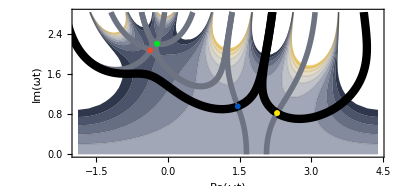

```mathematica
Block[{θx=π/12,px=2.5,
ωtmin=-3/5 π,ωtmax=7/5 π,ωtimin=0,ωtimax=0.9π,
plot,saddles,integrationlines},

(*Find saddles and calculate integration lines*)
saddles=<|"label"->#[[2]],"θ"->θx,"p"->px,"ωt"->#[[1]]|>&/@ClassifySaddles[FindSaddles[θx,px,"X"],θx,"X","2ω"];
integrationlines=FindIntegrationLines[saddles];

Show[{
cleanContourPlot[ContourPlot[
(-Im[Sv[ωtreal+ⅈ ωtimag,θx,px,"X"]/ω]/.config)/18,
{ωtreal,ωtmin,ωtmax},{ωtimag,ωtimin,ωtimax}
,ColorFunction->"GrayYellowTones"
,ContourStyle->Opacity[0.1]
,PlotRange->{-10,10}
]],

(*Drawing the steepest ascent/descent lines for all saddle points*)
PlotIntegrationLineAlongSaddle[#,Directive[{Lighter[testgrey,0.3],Thickness[0.01]}]]&/@Select[saddles,RegionMember[Rectangle[{ωtmin,ωtimin},{ωtmax,ωtimax}],ReIm@#[["ωt"]]]&],

(*Drawing the integration path lines*)
Graphics[{Directive[{Black,Thickness[0.015]}],#[["line"]]}]&/@integrationlines,

(*Plot the saddle points as markers in their respective colour*)
ListPlot[{(ReIm[#[["ωt"]]])},PlotStyle->LabelColors[[#[["label"]]]],PlotMarkers->{Automatic, 0.1}]&/@saddles,

Graphics[{}]
}
,Frame->True,FrameStyle->Black
,PlotRange->{{ωtmin,ωtmax},{ωtimin,ωtimax}}
,PlotRangeClipping->True
,AspectRatio->140/300(*Automatic*)
(*,ImageSize->columnWidth/2*)
,Axes->True,Method->{"AxesInFront"->False}, FrameLabel->{"Re(ωt)","Im(ωt)"}
,PlotRangePadding->None

]]
```

```mathematica
LabelColors
```

<|A→RGBColor[0.932, 0.28600000000000003, 0.1925],B→RGBColor[0, 0.9, 0.13],C→RGBColor[0., 0.34, 0.74375],D→RGBColor[1, 0.9, 0]|>

#### Action landscape at the coalescence

somethings wrong here in FindStep[]: {{A,-1,V4},{A,-1,B}}

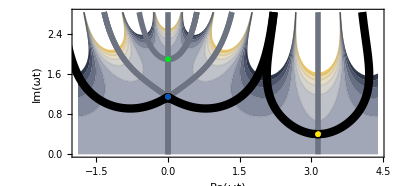

```mathematica
Block[{θx=FoldPointθ[["θ"]],px=0,
ωtmin=-3/5 π,ωtmax=7/5 π,ωtimin=0,ωtimax=0.9π,
plot,saddles,integrationlines},

(*Find saddles and calculate integration lines*)
saddles=<|"label"->#[[2]],"θ"->θx,"p"->px,"ωt"->#[[1]]|>&/@ClassifySaddles[FindSaddles[θx,px,"X"],θx,"X","2ω"];
integrationlines=FindIntegrationLines[saddles];

Show[{
cleanContourPlot[ContourPlot[
(-Im[Sv[ωtreal+ⅈ ωtimag,θx,px,"X"]/ω]/.config)/18,
{ωtreal,ωtmin,ωtmax},{ωtimag,ωtimin,ωtimax}
,ColorFunction->"GrayYellowTones"
,ContourStyle->Opacity[0.1]
,PlotRange->{-10,10}
]],

(*Drawing the steepest ascent/descent lines for all saddle points*)
PlotIntegrationLineAlongSaddle[#,Directive[{Lighter[testgrey,0.3],Thickness[0.01]}]]&/@Select[saddles,RegionMember[Rectangle[{ωtmin,ωtimin},{ωtmax,ωtimax}],ReIm@#[["ωt"]]]&],

(*Drawing the integration path lines*)
Graphics[{Directive[{Black,Thickness[0.015]}],#[["line"]]}]&/@integrationlines,

(*Plot the saddle points as markers in their respective colour*)
ListPlot[{(ReIm[#[["ωt"]]])},PlotStyle->LabelColors[[#[["label"]]]],PlotMarkers->{Automatic, 0.1}]&/@saddles,

Graphics[{}]
}
,Frame->True,FrameStyle->Black
,PlotRange->{{ωtmin,ωtmax},{ωtimin,ωtimax}}
,PlotRangeClipping->True
,AspectRatio->140/300(*Automatic*)
(*,ImageSize->columnWidth/2*)
,Axes->True,Method->{"AxesInFront"->False},FrameLabel->{"Re(ωt)","Im(ωt)"}
,PlotRangePadding->None

]]
```

## Field Transitions

#### Settings

```mathematica
mybeam1color=RGBColor["#b93a32"]
```

RGBColor[0.7254901960784313, 0.22745098039215686, 0.19607843137254902]

```mathematica
mybeam2color=RGBColor["#4C6A92"]
```

RGBColor[0.2980392156862745, 0.41568627450980394, 0.5725490196078431]

#### Plot for arbitrary field configuration

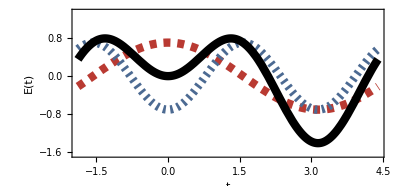

```mathematica
Block[{θx=π/4,
ωtmin=-3/5 π,ωtmax=7/5 π,ωtimin=0,ωtimax=0.9π,
maxEvalue,minEvalue},

maxEvalue=1.2;(*Max[Table[
FindMaximum[Evaluate[f[ωt]/.E0->1],ωt][[1]],{f,{(field1[#,θx,"X"])&,field2[#,θx,"X"]&,combinedfield[#,θx,"X"]&}}]];*)
minEvalue=-1.5;(*combinedfield[π,θx,"X"]/.E0->1;*)
(*Print[maxEvalue];*)

Show[{
Plot[Evaluate@({field1[ωt,θx,"X"],field2[ωt,θx,"X"],combinedfield[ωt,θx,"X"]}/.E0->1),{ωt,ωtmin,ωtmax}, PlotStyle->{{mybeam1color,Dashed,Thickness[0.015]},
{mybeam2color,Dashing[{0.005,0.008}],Thickness[0.015]},
{Thick,Black,Thickness[0.015]},Green}],

Graphics[{}]
}

,Frame->True,FrameStyle->Black
,PlotRange->{{ωtmin,ωtmax},{minEvalue-0.15,maxEvalue+0.15}}
,AspectRatio->140/300(*Automatic*)

,Axes->True,Method->{"AxesInFront"->False},FrameLabel->{"t","E(t)"}
,PlotRangePadding->None
]
]
```

## Save a figure

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"fig1.png"}],fig1,ImageResolution->600]
```

/home/anne/OneDrive/HHG-simulation-classical/Mathematica-Notebooks/2023-09 paper-fig/fig1.png